```mathematica
ResourceFunction["MaTeXInstall"][]
ConfigureMaTeX["Ghostscript" -> "C:\\Program Files\\gs\\gs9.53.3\\bin\\gswin64c.exe"]
```

PacletObject[…]

ConfigureMaTeX[Ghostscript→C:\Program Files\gs\gs9.53.3\bin\gswin64c.exe]

# Esercitazione Costruzioni in Acciaio

## Angolo travi di copertura

```mathematica
α = N[ArcTan[1/8]]
```

0.124355

## Pendenza copertura in percentuale

```mathematica
N[1/8]*100
```

12.5

# Analisi dei carichi

## Categoria H

```mathematica
qcatH  = 0.5;
```

## Carico neve

```mathematica
qsk = 2*.8;
```

## Carico vento - direzione parallela al colmo

## Copertura

```mathematica
qwkcop = 0.86;
```

## Pareti frontali

```mathematica
qwkfront = .85;
```

## Pareti laterali - depressione

```mathematica
qwklat = .61;
```

## Pannello di tamponamento laterale (Isofire Wall)

Spessore pannello 50mm. Il pannello deve sopportare il carico da vento in combinazione SLU

```mathematica
1.5*Max[qwklat, qwkfront]
```

1.275

Si sceglie un pannello con lamiera di spessore 5mm e portata 140 kg/m^2, spessore del pannello di 60mm e interasse massimo 2.45m. Il peso del pannello è 14.2 kg/m^2

```mathematica
gpannLat = 14.2*9.81/1000
```

0.139302

## Pannello di copertura

Pannello Isopan modello Isocop con interasse 1200mm. Assumendo un pannello di spessore nominale 50mm con lamiera da 0.5mm, il peso del pannello è di 10.7 kg/m^2. La combinazione agli SLU per combinazione con carico da neve principale è [kN/m^2]

```mathematica
1.5*qsk*Cos[α]^2-0*0.6*qwkcop + 1.5*0*qcatH
```

2.36308

In kg/m^2:

```mathematica
%*10^3/9.81
```

240.884

Con lamiere di 0.5mm, spessore nominale del pannello 50mm e portata massima di 250 kg/m^2 l’interasse massimo è di 205cm > 202cm. Allora, il peso del pannello di copertura è

```mathematica
qpannCop = 10.7*9.81/10^3
```

0.104967

# Baraccature

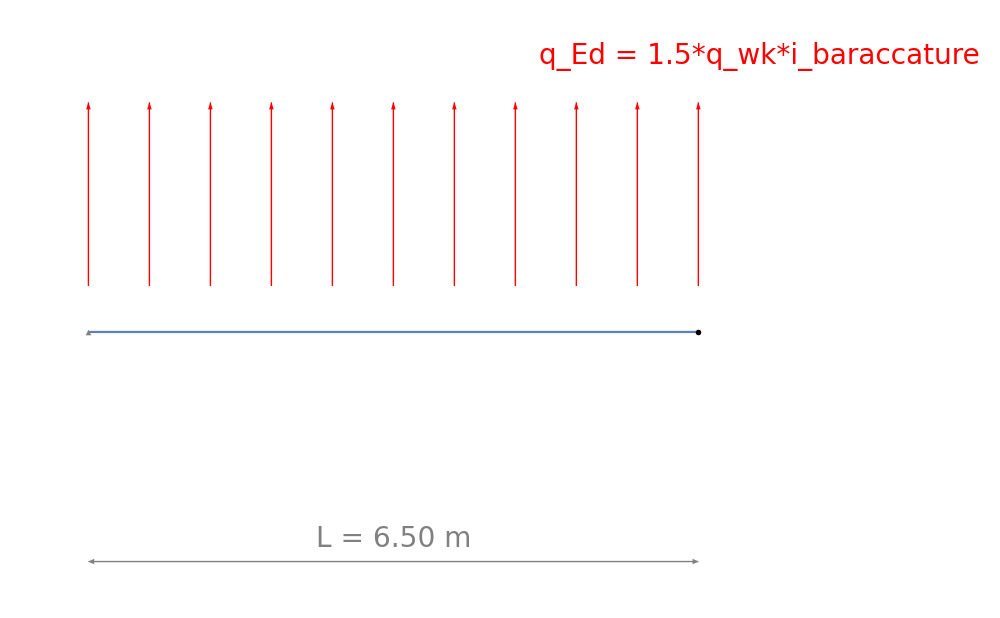

```mathematica
apph=Graphics[{Gray,Triangle[{{-0.5,-1},{0,0},{0.5,-1}}]}];
incv=Graphics[{Gray,Rectangle[{-0.5,-0.5},{0,0.5}]}];
carrh = Graphics[{
Gray,Triangle[{{-0.5,-1},{0,0},{0.5,-1}}],
Gray, Rectangle[{-.5,-1.3}, {.5, -1.8}],
Gray, Circle[{-.2,-1.15},.15],
Gray, Circle[{.2,-1.15},.15]
}];
L=1;h=0.01;
Show[
{Plot[0, {x,0,L},
PlotRange->{{-.5*L, 1.6*L}, {-.2, .2}},
Axes->False,
ScalingFunctions->"Reverse"],
Graphics[{Inset[carrh, {L,0},{0,0}, Scaled[.15]]}],
Graphics[{Inset[apph, {0,0}, {0,0}, Scaled[.1]]}],
Graphics[{Red,Arrowheads[0.02],Table[Arrow[{{i,0.02},{i,0.1}}],{i,0,L,L/10}]}],
Graphics[Text[Style["q_Ed = 1.5*q_wk*i_baraccature",Italic,Red,28],{L+.10,.12}]], 
Graphics[{Gray, Arrowheads[{-.02, .02}], Arrow[{{0, -.1}, {L, -.1}}]}], 
Graphics[Text[Style["L = 6.50 m", Italic, Gray, 28], {L/2, -.09}]]
}, ImageSize->{1000, 500}]
```

L’interasse tra le baraccature è di 2.20m

```mathematica
iBarac = 2.2;
dinfluenzaBarac = 1.1*iBarac;(*0.5*L + 0.6*L*)
LBarac = 6.5*10^3;
qEdyBarac = 1.5*Max[qwkfront, qwklat]*dinfluenzaBarac
MEdyBarac=qEdyBarac* LBarac^2/8 (*Nmm*)
MEdyBarac*10^-6
```

3.0855

1.62953×10^7

16.2953

Rispetto all’asse debole z-z agisce solo il peso del pennello di tamponamento laterale:

```mathematica
qEdzBarac = 1.5*gpannLat*iBarac
MEdzBarac = qEdzBarac*LBarac^2/8
MEdzBarac*10^-6
```

0.459697

2.42777×10^6

2.42777

## UPE 120 (classe 1 flessione e compressione)

```mathematica
Mpl[Wpl_, fy_] := Wpl*fy/1.05
NplRd[A_, fy_]:=A*fy/1.05

Es = 210*10^3;
Gs = Es/(2(1+.3));
JyBarac = 364*10^4;
JzBarac = 55.5*10^4;
WelyBarac = 60.60*10^4;
WplyBarac = 70.30*10^3;
WelzBarac= 13.80*10^4;
WplzBarac = 24.80*10^3;
AvzBarac = 7.18*10^2;
JtBarac = 2.9*10^4;
JωBarac = 1.12*10^9;
hBarac = 120;
bBarac = 60;
twBarac = 5;
tfBarac = 8;
dBarac = 80;
ABarac = 15.4*10^2;
fy = 355;
```

## Verifica di resistenza a flessione

L’inflessione che avviene rispetto all’asse forte è

```mathematica
MplyBarac = Mpl[WplyBarac, fy]
If[MplyBarac > MEdyBarac, TextCell["Verificato!", "Section"], TextCell["Non verificato!", "Section"]]
```

2.37681×10^7

Verificato!

Mentre rispetto all’asse debole

```mathematica
MplzBarac = Mpl[WplzBarac, fy]
If[MplzBarac > MEdzBarac, TextCell["Verificato!", "Section"], TextCell["Non verificato!", "Section"]]
```

8.38476×10^6

Verificato!

## Verifica per instabilità latero-torsionale

### Calcolo del momento critico

Il momento critico elastico per un profilo con un asse di simmetria non è definito in letteratura. Da un FEA con EF di tipo shell e una pressione uniforme pari a (3.1 N/mm)/(60mm)= 0.052 MPa, l’autovalore relativo al primo modo di instabilità è 1.7469 che corrisponde a un momento critico
M_cr = 1.7469*3.1*6.5^2/8= 28.6 kNm

```mathematica
Ncr[EJ_, l0_]:=(π^2*EJ)/l0^2


McrBarac = 28.6*10^6;

(*Snellezza adimensionale, dove Subscript[W, y] =Subscript[W, pl,z]*)
λLT[Wy_, fy_, Mcr_] := Sqrt[(Wy*fy)/Mcr]
λLTBarac = λLT[WplyBarac, fy, McrBarac]
```

0.934133

L’instabilità latero-torsionale può essere ignorata se
λ_LT≤ λ_(LT,0)
o
M_Ed/M_cr≤ (λ_(LT,0))^2

```mathematica
λLTBarac≤ .4
MEdyBarac/McrBarac≤ (.4)^2
```

False

False

è necessario fare la verifica per instabilità latero - torsionale dell' arcareccio.

### Verifica per instabilità latero-torsionale dell’arcareccio

```mathematica
λLT0 = .2;
ϕLT[αlt_, λlt_]:=.5*(1+αlt*(λlt-λLT0)+λlt^2)
αLTBarac = .76; (*Sezioni diverse dalle sezioni ad "I"*)
ϕLTBarac = ϕLT[αLTBarac, λLTBarac]

χLT[ϕlt_, λlt_]:=Min[1/(ϕlt+√(ϕlt^2-λlt^2)), 1]
χLTBarac = χLT[ϕLTBarac, λLTBarac]

MbRd[χlt_, Wy_, fy_]:=χlt*Wy*fy/1.05
MbRdBarac = MbRd[χLTBarac,WplyBarac, fy];
MbRdBarac*10^-6
MEdyBarac*10^-6

If[MbRdBarac ≥ MEdyBarac, Print[TextCell["Verificato!", "Section"]], Print[TextCell["Non Verificato!", "Section"]]]
```

1.21527

0.501849

11.928

16.2953

Non Verificato!

La verifica per instabilità latero-torsionale non è soddisfatta!
Vedi LTB.nb per la verifica con montante verticale

```mathematica
qEdyBarac*(LBarac/2)^2/8*10^-6
```

4.07382

# Arcarecci

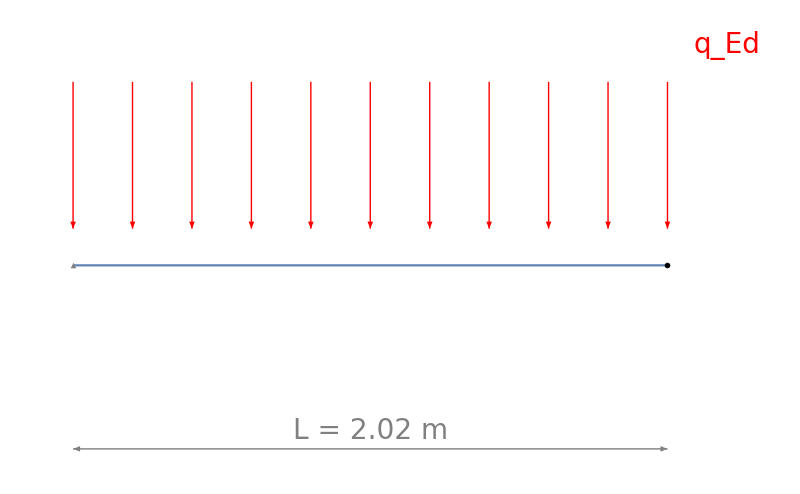

```mathematica
apph=Graphics[{Gray,Triangle[{{-0.5,-1},{0,0},{0.5,-1}}]}];
incv=Graphics[{Gray,Rectangle[{-0.5,-0.5},{0,0.5}]}];
carrh = Graphics[{
Gray,Triangle[{{-0.5,-1},{0,0},{0.5,-1}}],
Gray, Rectangle[{-.5,-1.3}, {.5, -1.8}],
Gray, Circle[{-.2,-1.15},.15],
Gray, Circle[{.2,-1.15},.15]
}];
L=1;h=0.01;
trave = {Plot[0, {x,0,L},
PlotRange->{{-.5*L, 1.6*L}, {-.2, .2}},
Axes->False,
ScalingFunctions->"Reverse"],
Graphics[{Inset[carrh, {L,0},{0,0}, Scaled[.15]]}],
Graphics[{Inset[apph, {0,0}, {0,0}, Scaled[.1]]}],
Graphics[{Red,Arrowheads[0.02],Table[Arrow[{{i,0.1},{i,0.02}}],{i,0,L,L/10}]}],
Graphics[Text[Style["q_Ed",Italic,Red,28],{L+.10,.12}]], 
Graphics[{Gray, Arrowheads[{-.02, .02}], Arrow[{{0, -.1}, {L, -.1}}]}], 
Graphics[Text[Style["L = 2.02 m", Italic, Gray, 28], {L/2, -.09}]]};
Show [trave, ImageSize-> 800]
```

## Analisi dei carichi

HP arcarecci IPE 180

```mathematica
Garc = 18.8*9.81/10^3
```

0.184428

## Combinazione dei carichi

## SLU

### Combinazione 1: neve principale

```mathematica
iarc = 2.02;
dinfluenza = 1.15*iarc;
{qEd1arc,qEd1yarc,qEd1zarc}  = {1.3*Garc+ 1.5*qpannCop*dinfluenza + 1.5*qsk*dinfluenza*Cos[α]-0*0.6*qwkcop/Cos[α]*dinfluenza+1.5*0*qcatH, 
 (1.3*Garc+ 1.5*qpannCop*dinfluenza + 1.5*qsk*dinfluenza*Cos[α]-0*0.6*qwkcop/Cos[α]*dinfluenza+1.5*0*qcatH)*Cos[α],
(1.3*Garc+ 1.5*qpannCop*dinfluenza + 1.5*qsk*dinfluenza*Cos[α]-0*0.6*qwkcop/Cos[α]*dinfluenza+1.5*0*qcatH)*Sin[α]}
Fw1arc = .6*13.1 *10^3(*N di compressione sugli arcarecci*)
```

{6.13766,6.09027,0.761283}

7860.

### Combinazione 2: vento principale favorevole

```mathematica
{qEd2arc, qEd2yarc, qEd2zarc} = {
1*Garc + .8*qpannCop*dinfluenza -1.5*qwkcop/Cos[α]*dinfluenza+ 0*.5*qsk*dinfluenza*Cos[α] + 0*0*qcatH,
(1*Garc + .8*qpannCop*dinfluenza -1.5*qwkcop/Cos[α]*dinfluenza+ 0*.5*qsk*dinfluenza*Cos[α] + 0*0*qcatH)*Cos[α],
(1*Garc + .8*qpannCop*dinfluenza -1.5*0*dinfluenza+ 0*.5*qsk*dinfluenza*Cos[α] + 0*0*qcatH)*Sin[α]}
Fw2arc = 13.1*10^3 (*N di compressione sugli arcarecci*)
```

{-2.64049,-2.6201,0.047071}

13100.

### Combinazione 3: cat. H principale

```mathematica
{qEd3arc, qEd3yarc, qEd3zarc} = {
1.3*Garc+ 1.5*qpannCop*dinfluenza +1.5*qcatH+ 1.5*.5*qsk*dinfluenza*Cos[α] - 0*0.6*qwkcop/Cos[α]*dinfluenza,
(1.3*Garc + 1.5*qpannCop*dinfluenza +1.5*qcatH+ 1.5*.5*qsk*dinfluenza*Cos[α] - 0*0.6*qwkcop/Cos[α]*dinfluenza)*Cos[α],
(1.3*Garc + 1.5*qpannCop*dinfluenza +1.5*qcatH+ 1.5*.5*qsk*dinfluenza*Cos[α] - 0*0.6*qwkcop/Cos[α]*dinfluenza)*Sin[α]}
Fw3arc = .6*13.1 *10^3(*N di compressione sugli arcarecci*)
```

{4.12159,4.08976,0.51122}

7860.

```mathematica
{4.121587720627021,4.089760312112905,0.5112200390141132}
```

{4.12159,4.08976,0.51122}

### Carico di progetto arcarecci

```mathematica
qEdarc = Max[qEd1arc, qEd2arc, qEd3arc]
qEdyarc = Max[qEd1arc*Cos[α], qEd2yarc, qEd3yarc]
qEdzarc = Max[qEd1arc*Sin[α], qEd2zarc, qEd3zarc]
```

6.13766

6.09027

0.761283

## SLE Rara

### Combinazione 1: neve principale

```mathematica
iarch = 2.02;
dinfluenza = 1.15*iarch;
qEd1rara = 1*Garc+ 1*qpannCop*dinfluenza + qsk*dinfluenza*Cos[α]-0.6*qwkcop/Cos[α]*dinfluenza+0*qcatH
qEd1yrara = qEd1rara*Cos[α]
qEd1zrara = qEd1rara*Sin[α]
Fwarch1rara = .6*13.1/1.5 *10^3(*N di compressione sugli arcarecci*)
```

2.90837

2.88591

0.360739

5240.

### Combinazione 2: vento principale favorevole

```mathematica
{qEd2rara, qEd2yrara, qEd2zrara} = {
1*Garc + qpannCop*dinfluenza -qwkcop/Cos[α]*dinfluenza+ .5*qsk*dinfluenza*Cos[α] + 0*qcatH,
(1*Garc + qpannCop*dinfluenza -qwkcop/Cos[α]*dinfluenza+ .5*qsk*dinfluenza*Cos[α] + 0*qcatH)*Cos[α],
(1*Garc + qpannCop*dinfluenza -0*qwkcop/Cos[α]*dinfluenza+ .5*qsk*dinfluenza*Cos[α] + 0*qcatH)*Sin[α]}
Fwarch2rara = 13.1/1.5 *10^3(*kN di compressione sugli arcarecci*)
```

{0.258988,0.256988,0.281846}

8733.33

### Combinazione 3: cat. H principale

```mathematica
{qEd3rara, qEd3yrara, qEd3zrara} = {
Garc +qpannCop*dinfluenza +qcatH+ .5*qsk*dinfluenza*Cos[α] - 0.6*qwkcop/Cos[α]*dinfluenza,
(Garc +qpannCop*dinfluenza +qcatH+ .5*qsk*dinfluenza*Cos[α] - 0.6*qwkcop/Cos[α]*dinfluenza)*Cos[α],
(Garc +qpannCop*dinfluenza +qcatH+ .5*qsk*dinfluenza*Cos[α] - 0*0.6*qwkcop/Cos[α]*dinfluenza)*Sin[α]}
```

{1.56432,1.55224,0.343863}

### Carico di progetto arcarecci

```mathematica
qEdarcrara = Max[qEd1rara, qEd2rara, qEd3rara]
qEdyarcrara = qEd1yrara
qEdzarcrara = qEd1zrara
```

2.90837

2.88591

0.360739

## Verifiche di resistenza arcareccio

Gli arcarecci sono soggetti a presso-flessione biassiale! La verifica di resistenza va fatta secondo il punto 6.2.9 del EC3. L’azione assiale agente sull’arcareccio non è la F_Ed calcolata in  precedenza (i.e. F_Ed= 13.1 kN per la combo 2) ma sarà minore, poiché parte della sollecitazione è assorbita dai controventi. Il sistema da analizzare è il seguene

-Graphics-

Usando come controventi dei profili a “L” 120x120x15 (classe 1 in compressione pura) le azioni interne risultano:

-Graphics-

IPE 180 (classe 1 a flessione, classe 2 a compressione):

```mathematica
ClearAll[MEdyarc, MEdzarc , VEdyarc, VEdzarc, Mpl, Vpl, fy, Wplyarc, Wplzarc, Aarc, darc, twarc, Es, harc, barc]
Es = 210*10^3;
Gs = Es/(2(1+.3));
Larc = 6.5*10^3;
Jzarc = 100.8*10^4;
Jyarc = 1316*10^4;
Jtarc = 4.726*10^4 ;
Jωarc = 7.431*10^9;
Wplyarc = 166.4*10^3;
Welyarc = 146.3*10^3;
Wplzarc = 34.59*10^3;
Welzarc = 22.16*10^3;
fy = 355;
Aarc = 23.9*10^2;
Avarc = 11.25*10^2;
darc = 146;
twarc = 5.3;
tfarc = 8.;
harc=180;
barc = 91;

NEdarc = 7.17*10^3 (*N*)
MEdyarc = qEdyarc*Larc^2/8
MEdzarc = qEdzarc*Larc^2/8
VEdyarc = qEdyarc*Larc/2
VEdzarc = qEdzarc*Larc/2
NplRd[A_, fy_]:= A *fy/1.05;
Mpl[Wpl_, fy_] := (Wpl*fy)/1.05
Vpl[Av_, fy_]:= (Av*fy/(√3))/1.05
```

7170.

3.21642×10^7

4.02053×10^6

19793.4

2474.17

## Compressione

```mathematica
Ncr[EJ_, l0_]:=(π^2*EJ)/l0^2
NplRdarc = NplRd[Aarc, fy]
{Ncryarc,Ncrzarc }= {Ncr[Es*Jyarc, Larc], Ncr[Es*Jzarc, Larc]}
{λyarc, λzarc} = {Sqrt[Aarc*fy/Ncryarc], Sqrt[Aarc*fy/Ncrzarc]}
αyarc = If[harc/barc≤1.2, .34, .21]
αzarc = If[harc/barc≤1.2, .49, .34]
{ϕyarc, ϕzarc} = .5*(1+{αyarc, αzarc}*({λyarc, λzarc}-.2)+({λyarc, λzarc})^2)
{χyarc, χzarc} = 1/({ϕyarc, ϕzarc}+Sqrt[({ϕyarc, ϕzarc})^2-({λyarc, λzarc})^2])
{NbRdyarc, NbRdzarc} = {χyarc, χzarc} *(Aarc*fy)/1.05
If[NEdarc≤ Min[NplRdarc,NbRdyarc, NbRdzarc], TextCell["Verificato!", "Section"]]
```

808048.

{645577.,49448.5}

{1.14641,4.14225}

0.21

0.34

{1.2565,9.74932}

{0.564707,0.0538361}

{456310.,43502.1}

Verificato!

## Flessione

```mathematica
{MplRdyarc, MplRdzarc} = {Mpl[Wplyarc,fy], Mpl[Wplzarc,fy]}
If[MEdyarc≤ MplRdyarc && MEdzarc≤ MplRdzarc, TextCell["Verificato!", "Section"]]
```

{5.6259×10^7,1.16947×10^7}

Verificato!

## Taglio

```mathematica
VcRdarc = Vpl[Avarc, fy]
If[VcRdarc ≥ Max[VEdyarc, VEdzarc], TextCell["Verificato!", "Section"]]
If[Max[VEdyarc, VEdzarc] < .5*VcRdarc, TextCell["Effetto del taglio trascurabile!", "Section"]]
```

219599.

Verificato!

Effetto del taglio trascurabile!

Poiché V_Ed< 0.5 V_(c,Rd) allora è sufficiente la verifica a presso-flessione, senza contare il contributo del taglio (p.to 6.2.8 (2) EC3)

## Presso-flessione

```mathematica
NplRdarc = Aarc*fy/1.05
NEdarc ≤ .25 NplRdarc
NEdarc≤ (0.5*darc*twarc)/1.05*fy
NEdarc ≤ (darc*twarc)/1.05*fy
```

808048.

True

True

True

L’azione assiale non ha effetti significativi!

Si può comunque fare la verifica:

```mathematica
MplyRdarc = Mpl[Wplyarc, fy];
MplzRdarc = Mpl[Wplzarc, fy];
aarc = Min[(Aarc-2*barc*tfarc)/Aarc, .5];
MNyRdarc = Min[MplyRdarc*(1-NEdarc/NplRdarc)/(1-.5*aarc), MplyRdarc]
MNzRdarc = If[NEdarc/NplRdarc≤ aarc, MplzRdarc, MplzRdarc*(1-((NEdarc/NplRdarc-aarc)/(1-aarc))^2)]
If[(MEdyarc/MNyRdarc)^2+(MEdzarc/MNzRdarc)^Max[5*NEdarc/NplRdarc,1]≤1, TextCell["Verificato!", "Section"]]
```

5.6259×10^7

1.16947×10^7

Verificato!

## Verifiche di stabilità arcareccio senza ritegni laterali

```mathematica
1000*√((.5)^3)*(50+10*(1200)^(1/3))*2020/50≥ (Es*Jωarc*π^2/Larc^2+Gs*Jtarc+Es*Jzarc*π^2/Larc^2*.25*harc^2)*70/harc^2
```

False

-Graphics-

Il pannello di copertura non ha sufficiente rigidezza da vincolare lateralmente gli arcarecci
Prima di effettuare la verifica di stabilità per presso-flessione (6.3.3 EC3), va verificato che la l’elemento non sia suscettibile a distorsioni (instabilità latero-torsionale).

## Instabilità latero-torsionale

### Calcolo del momento critico

N_(cr,T) = A/(J_y+J_z)[G J_t + (π^2 E J_ω)/L^2]
N_(Ed,max)= N_Ed^(combo 2) = 8.57 kN < 707.25 kN

Il momento critico che non tiene conto dello sforzo assiale (N_Ed=0) è [kN m]
M_cr=C_1[π/L √(G J_t E J_z(1+(π^2 E J_ω)/(L^2 G J_t)))]

Il momento critico elastico per instabilità L-T, che tiene conto dello sforzo assiale di compressione è
M_(cr,N)=C_1[π/L √(G J_t E J_z(1+(π^2 E J_ω)/(L^2 G J_t)))]√((1-N_Ed/(N_(cr,z)))(1-N_Ed/(N_(cr,T))))

Dal software agli EF LTBeamN il valore che si ricava è
M_(max,cr) = 15.61 kN m
-Graphics-

```mathematica
ClearAll[NcrT, Ncr, McrLT, McrN, λLT]
Ncr[EJ_, l0_]:=(π^2*EJ)/l0^2
Ncrzarc = Ncr[Es*Jzarc, Larc]
Ncryarc = Ncr[Es*Jyarc, Larc]

NcrT[A_, Jy_, Jz_, G_, Jt_, Ee_, Jω_, L_]:=A/(Jy+Jz)*(G*Jt+(π^2*Ee*Jω)/L^2);
NcrTarc = NcrT[Aarc,Jyarc,Jzarc,Gs,Jtarc , Es,Jωarc, Larc]

McrLT[C1_, L_, G_, Jt_, Ee_, Jz_, Jω_]:=C1*(π/L*Sqrt[G*Jt*Ee*Jz*(1+(π^2*Ee*Jω)/(L^2*G*Jt))]); (*Subscript[N, Ed]=0*)

McrN[C1_, L_, G_, Jt_, Ee_, Jz_, Jω_, NEd_, Ncrz_, NcrT_]:=C1*(π/L*Sqrt[G*Jt*Ee*Jz*(1+(π^2*Ee*Jω)/(L^2*G*Jt))])*Sqrt[(1-NEd/Ncrz)*(1-NEd/NcrT)]; (*Subscript[N, Ed]≠ 0*)
(*HP: 
carico agente sul centro di taglio: zg = 0
diagramma dei momenti di una trave appoggiata soggetta a un carico distribuito: C1 = 1.132, C2 = 0.459, C3 = 0.525
*)
C1arc = 1.132;

McrNarc = McrN[C1arc, Larc, Gs, Jtarc , Es, Jzarc, Jωarc, NEdarc, Ncrzarc, NcrTarc]

(*Snellezza adimensionale, dove Subscript[W, y] =Subscript[W, pl,y]*)
λLT[Wy_, fy_, Mcr_] := Sqrt[(Wy*fy)/Mcr];
λLTarc = λLT[Wplyarc, fy, McrNarc]
```

49448.5

645577.

705409.

1.49749×10^7

1.98614

L’instabilità latero-torsionale può essere ignorata se
λ_LT≤ λ_(LT,0)
o
M_Ed/M_cr≤ (λ_(LT,0))^2

```mathematica
λLTarc ≤ .4
(MEdyarc*10^6)/McrNarc≤ (.4)^2
```

False

False

è necessario fare la verifica per instabilità latero - torsionale dell' arcareccio.

### Verifica per instabilità latero-torsionale dell’arcareccio

La distribuzione del momento flettente è quella tipica per la trave appoggiata, allora
k_c= 0.94 
e quindi
f = 1-0.5(1-k_c)[1-2.0(λ_LT - 0.8)^2]

Allora 
χ_(LT,mod) = χ_LT/f ≤ [1, 1/λ_LT^2]

```mathematica
f[kc_, λlt_]:= Min[1-.5*(1-kc)*(1-2*(λlt-.8)^2), 1]
farc = f[.94, λLTarc]

λLT0 = .2;
β=1;
ϕLT[αlt_, λlt_]:=.5*(1+αlt*(λlt-λLT0)+β*λlt^2)
(*
Per calcolare Subscript[α, LT] con il metodo per sezioni laminate (non il metodo generale!) si deve usare la Table 6.5 del EC3 (non la 6.4!). 
*)
αLTarc = If[harc/barc≤2, .34, .49]
ϕLTarc = ϕLT[αLTarc, λLTarc]

χLT[ϕlt_, λlt_]:=Min[1/(ϕlt+√(ϕlt^2-λlt^2)), 1]
χLTarc = Min[χLT[ϕLTarc, λLTarc]/farc, 1/λLTarc^2, 1]

MbRd[χlt_, Wy_, fy_]:=χlt*Wy*fy/1.05
MbRdarc = MbRd[χLTarc,Wplyarc, fy]

If[MbRdarc ≥ Max[MEdyarc, MEdzarc], Print[TextCell[ "Verificato!", "Section"]], Print[TextCell["Non Verificato!", "Section"]]]
```

1

0.34

2.77601

0.212068

1.19307×10^7

Non Verificato!

```mathematica
MbRdarc*10^-6
MEdyarc*10^-6
MEdzarc*10^-6
```

11.315

32.1642

4.02053

La verifica per instabilità latero-torsionale non è soddisfatta!

## Verifiche di deformabilità senza ritegni laterali

```mathematica
δmax[q_, l_, EJ_]:= 5/384*(q*l^4)/EJ
```

Rispetto all’asse forte

```mathematica
δmax[qEdyarcrara, Larc, Es*Jyarc]≤ 6500/200
δmax[qpannCop*dinfluenza*Cos[α] , Larc, Es*Jyarc]≤ 6500/250
```

True

True

Rispetto all’asse debole

```mathematica
δmax[qEdzarcrara, Larc, Es*Jzarc]≤ 6500/200
δmax[qpannCop*dinfluenza*Sin[α] , Larc, Es*Jzarc]≤ 6500/250
```

False

True

I pendini sono necessari anche per la verifica di deformabilità.

## Verifiche di stabilità arcareccio con ritegni laterali

-Graphics-

Lo schema statico dell’arcareccio è una trave su tre appoggi, simmetrica e caricata simmetricamente. Può essere, perciò, presa in considerazione solamente metà trave, schematizzata come una trave appoggio - incastro. La lunghezza di libera inflessione allora vale:
L_0 = 0.7 L

```mathematica
L0arc = .7*Larc/2
```

2275.

## Instabilità latero-torsionale

### Calcolo del momento critico

N_(cr,T) = A/(J_y+J_z)[G J_t + (π^2 E J_ω)/L^2]
N_(Ed,max)= N_Ed^(combo 2) = 8.57 kN < 707.25 kN

Il momento critico che non tiene conto dello sforzo assiale (N_Ed=0) è [kN m]
M_cr=C_1[π/L √(G J_t E J_z(1+(π^2 E J_ω)/(L^2 G J_t)))]

Il momento critico elastico per instabilità L-T, che tiene conto dello sforzo assiale di compressione è
M_(cr,N)=C_1[π/L √(G J_t E J_z(1+(π^2 E J_ω)/(L^2 G J_t)))]√((1-N_Ed/(N_(cr,z)))(1-N_Ed/(N_(cr,T))))

Dal software agli EF LTBeamN il valore che si ricava è
M_(max,cr) = 41.79 kN m
-Graphics-

```mathematica
Ncr[EJ_, l0_]:=(π^2*EJ)/l0^2
Ncrzarc = Ncr[Es*Jzarc, L0arc]
Ncryarc = Ncr[Es*Jyarc, Larc]

NcrT[A_, Jy_, Jz_, G_, Jt_, Ee_, Jω_, L_]:=A/(Jy+Jz)*(G*Jt+(π^2*Ee*Jω)/L^2)
NcrTarc = NcrT[Aarc,Jyarc,Jzarc,Gs,Jtarc , Es,Jωarc, L0arc]

McrLT[C1_, L_, G_, Jt_, Ee_, Jz_, Jω_]:=C1*(π/L*Sqrt[G*Jt*Ee*Jz*(1+(π^2*Ee*Jω)/(L^2*G*Jt))]) (*Subscript[N, Ed]=0*)

McrN[C1_, L_, G_, Jt_, Ee_, Jz_, Jω_, NEd_, Ncrz_, NcrT_]:=C1*(π/L*Sqrt[G*Jt*Ee*Jz*(1+(π^2*Ee*Jω)/(L^2*G*Jt))])*Sqrt[(1-NEd/Ncrz)*(1-NEd/NcrT)] (*Subscript[N, Ed]≠ 0*)
McrNarc = McrN[C1arc, L0arc, Gs, Jtarc , Es, Jzarc, Jωarc, NEdarc, Ncrzarc, NcrTarc]

(*Snellezza adimensionale, dove Subscript[W, y] =Subscript[W, pl,y]*)
λLT[Wy_, fy_, Mcr_] := Sqrt[(Wy*fy)/Mcr]
λLTarc = λLT[Wplyarc, fy, McrNarc]
```

403661.

645577.

1.1459×10^6

5.85638×10^7

1.00433

L’instabilità latero-torsionale può essere ignorata se
λ_LT≤ λ_(LT,0)
o
M_Ed/M_cr≤ (λ_(LT,0))^2

```mathematica
λLTarc ≤ .4
(MEdyarc*10^6)/McrNarc≤ (.4)^2
```

False

False

è necessario fare la verifica per instabilità latero - torsionale dell' arcareccio.

### Verifica per instabilità latero-torsionale dell’arcareccio

La distribuzione del momento flettente è quella tipica per la trave appoggio-incastro, allora
k_c= 0.91 
e quindi
f = 1-0.5(1-k_c)[1-2.0(λ_LT - 0.8)^2]

Allora 
χ_(LT,mod) = χ_LT/f ≤ [1, 1/λ_LT^2]

```mathematica
f[kc_, λlt_]:= Min[1-.5*(1-kc)*(1-2*(λlt-.8)^2), 1]
farc = f[.91, λLTarc]

λLT0 = .4;
ϕLT[αlt_, λlt_]:=.5*(1+αlt*(λlt-λLT0)+λlt^2)
αLTarc = If[harc/barc≤2, .34, .49];
ϕLTarc = ϕLT[αLTarc, λLTarc]

χLT[ϕlt_, λlt_]:=Min[1/(ϕlt+√(ϕlt^2-λlt^2)), 1]
χLTarc = Min[χLT[ϕLTarc, λLTarc]/farc, 1, 1/λLTarc^2]

MbRd[χlt_, Wy_, fy_]:=χlt*Wy*fy/1.05
MbRdarc = MbRd[χLTarc,Wplyarc, fy]
MEdyarc

If[MbRdarc ≥ MEdyarc, Print[TextCell["Verificato!", "Section"]], Print[TextCell["Non Verificato!", "Section"]]]
```

0.958758

1.10707

0.663142

3.73078×10^7

3.21642×10^7

Verificato!

La verifica per instabilità latero-torsionale è soddisfatta!

## Buckling presso-flessione

Una volta effettuata al verifica per instabilità latero-torsionale si procede con la verifica di buckling a presso-flessione. In questo caso il momento sollecitante rispetto all’asse debole non è più quello calcolato in precedenze ma varrà
M_(Ed,z,arc) = q_(Ed,z,arc)*(L_(0,arc))^2/8
che corrisponde al momento sull’appoggio centrale.

```mathematica
ClearAll[ Ncr,χ, ϕ, λ,A, EJ, l0, NbRd];
χ[ϕ_, λ_] := Min[1/(ϕ+Sqrt[ϕ^2-λ^2]), 1]
ϕ[α_, λ_]:= .5*(1+α*(λ-.2)+λ^2)
Ncr[EJ_, l0_]:=(π^2*EJ)/l0^2
λ[A_, fy_, Ncr_]:=Sqrt[A*fy/Ncr]
NbRd[χ_, A_,fy_]:= χ*(A*fy)/1.05

{Ncryarc, Ncrzarc} ={Ncr[Es*Jyarc, Larc],Ncr[Es*Jzarc, L0arc]}
{αyarc, αzarc} = If[harc/barc≤1.2 , {.34, .49}, {.21, .34}]
{λyarc, λzarc} = {λ[Aarc, fy, Ncryarc], λ[Aarc, fy, Ncrzarc]}
{ϕyarc, ϕzarc} = {ϕ[αyarc, λyarc], ϕ[αzarc, λzarc]}
{χyarc, χzarc} = {χ[ϕyarc, λyarc], χ[ϕzarc, λzarc]}
{NbRdyarc, NbRdzarc} = {NbRd[χyarc,Aarc,fy],NbRd[χzarc,Aarc,fy]} (*Valore in [N]*)
```

{645577.,403661.}

{0.21,0.34}

{1.14641,1.44979}

{1.2565,1.76341}

{0.564707,0.361368}

{456310.,292003.}

```mathematica
MEdzarc = qEdzarc*(L0arc)^2/8
NEdarc
```

492515.

7170.

La verifica è superata se sono soddisfatte le (6.61), (6.62) del EC3:

N_Ed/((χ_y N_Rk)/γ_m1) + k_yy *(M_(y,Ed + ΔM_(y,Ed)))/((χ_LT * M_(y.Rk))/γ_m1) + k_yz*(M_(z,Ed) + ΔM_(z,Ed))/((M_(z,Rk))/γ_m1)≤ 1

N_Ed/((χ_z N_Rk)/γ_m1) + k_zy *(M_(y,Ed + ΔM_(y,Ed)))/((χ_LT * M_(y.Rk))/γ_m1) + k_zz*(M_(z,Ed) + ΔM_(z,Ed))/((M_(z,Rk))/γ_m1)≤ 1

Usando il Metodo 1:

k_yy= C_my C_mLT *μ_y/(1-N_Ed/(N_(cr,y)))*1/C_yy
k_yz= C_mz *μ_y/(1-N_Ed/(N_(cr,z)))*1/C_yz*0.6 √(w_z/w_y)
k_zy= C_my C_mLT *μ_z/(1-N_Ed/(N_(cr,y)))*1/C_zy*0.6 √(w_y/w_z)
k_zz= C_mz *μ_z/(1-N_Ed/(N_(cr,z)))*1/C_zz
μ_y = (1-N_Ed/(N_(cr,y)))/(1-χ_y*N_Ed/(N_(cr,y)))
μ_z = (1-N_Ed/(N_(cr,z)))/(1-χ_z*N_Ed/(N_(cr,z)))
w_y = min{(W_(pl,y))/(W_(el,y)), 1.5}
w_z = min{(W_(pl,z))/(W_(el,z)), 1.5}
n_pl = N_Ed/(N_Rk/γ_m0)
a_LT = 1-J_T/J_y
C_yy = max{1+(w_y-1)*[(2-1.6/w_y C_my^2 λ_max- 1.6/w_y C_my^2 λ_max^2)*n_pl-b_LT], (W_(el,y))/(W_(pl,y))}
b_LT = 0.5*a_LT λ_0^2*(M_(y,Ed))/(χ_LT M_(pl,y,Rd))*(M_(z,Ed))/(M_(pl,z,Rd))
C_yz = max{1+(w_z-1)*[(2-14 C_mz^2 λ_max^2/w_z^5)*n_pl-c_LT], 0.6*√(w_z/w_y)(W_(el,z))/(W_(pl,z))}
c_LT = 10 a_LT*λ_0^2/(5+λ_z^4)*(M_(y,Ed))/(C_my χ_LT M_(pl,y,Rd))
C_zy = max{1+(w_y-1)*[(2-14 C_my^2 λ_max^2/w_y^5)*n_pl-d_LT], 0.6*√(w_y/w_z)(W_(el,y))/(W_(pl,y))}
d_LT = 2 a_LT*λ_0/(0.1+λ_z^4)*(M_(y,Ed))/(C_my χ_LT M_(pl,y,Rd))*(M_(z,Ed))/(C_mz M_(pl,z,Rd))
C_zz = max{1+(w_z-1)*(2-1.6/w_z C_mz^2 λ_max- 1.6/w_z C_mz^2 λ_max^2 - e_LT)*n_pl,(W_(el,z))/(W_(pl,z))}
e_LT = 1.7 a_LT *λ_0^2/(0.1+λ_z^4)*(M_(y,Ed))/(C_my χ_LT M_(pl,y,Rd))
λ_max = max{λ_y, λ_z}
λ_0 ∈ [0.2, 0.4]

Se λ_0 ≤ λ_(0,LIM) = 0.2 √C_1*((1-N_Ed/(N_(cr,z)))(1-N_Ed/(N_(cr,T))))^(1/4) le deformazioni torsionali sono trascurabili e C_my = C_(my,0) (vedi Table A.2)
C_1 = k_c^-2 con k_c da Table 6.6

Se λ_0 > λ_(0,LIM) = 0.2 √C_1*((1-N_Ed/(N_(cr,z)))(1-N_Ed/(N_(cr,T))))^(1/4) le deformazioni torsionali non sono trascurabili e:
	C_my = C_(my,0) + (1-C_(my,0))*(√ϵ_y a_LT)/(1+√ϵ_y a_LT)
	C_mz = C_(mz,0)
	C_mLT = max{C_my^2*a_LT/(√((1-N_Ed/(N_(cr,z)))(1-N_Ed/(N_(cr,T))))), 1}
	con ϵ_y = (M_(y,Ed))/N_Ed*A/(W_(el,y)) per sezioni di classe 1,2,3.

```mathematica
kcarc = .91;
C1arc = kcarc^-2;
If[.2 ≤ .2*√C1arc*((1-NEdarc/Ncrzarc)*(1-NEdarc/NcrTarc))^(1/4), TextCell["Deformazioni torsionali trascurabili", "Subsubsection"], TextCell["Deformazioni torsionali NON trascurabili","Subsubsection"]]
```

Deformazioni torsionali trascurabili

Lungo l’asse forte lo schema statico è di trave semplicemente appoggiata:
C_(my,0) = 1+0.03*N_Ed/(N_(cr,y))
mentre rispetto all’asse z-z, lo schema è ad incastro-appoggio:
C_(mz,0) = 1+((π^2*EJ_z*|δ_x|)/(L^2*|M_(z,Ed)(x)|)-1)*N_Ed/(N_(cr,z)) con δ_x lo spostamento massimo in campata e M_(z,Ed)(x) il massimo momento che si sviluppa (ql^2/8 sull'incastro)

```mathematica
ϵy[MEdy_, NEd_, A_, Wely_] := MEdy/NEd*A/Wely (*deformazioni torsionali non trascurabili*)
aLT[Jt_, Jy_] := Max[1-Jt/Jy, 0]
(*Cmy[Cmy0_, ϵy_, aLT_] := Cmy0 + (1-Cmy0)*(√ϵy*aLT)/(1+√ϵy*aLT)  deformazioni torsionali non trascurabili*)
(*CmLT[Cmy_, aLT_, NEd_, Ncrz_, NcrT_] := Max[Cmy^2*aLT/(√((1-NEd/Ncrz)*(1-NEd/NcrT))), 1] deformazioni torsionali non trascurabili*)
w[Wply_, Wely_]:=Min[Wply/Wely, 1.5]
Ncr[EJ_, L0_]:= π^2*EJ/L0^2
λ[A_, fy_, Ncr_]:=√((A*fy)/Ncr)
λmax[λy_, λz_] := Max[λy, λz]
npl[NEd_, NRk_]:= NEd/(NRk/1.05)
bLT[aLT_, λ0_, MyEd_,χLT_, MplyRd_, MzEd_, MplzRd_]:= .5*aLT*λ0^2*MyEd/(χLT * MplyRd)*MzEd/MplzRd
Cyy[wy_, Cmy_, λmax_, npl_, bLT_, Wely_, Wply_]:=Max[1+(wy-1)*((2-1.6/wy*Cmy^2*λmax-1.6/wy*Cmy^2*λmax^2)*npl-bLT), Wely/Wply]
μ[NEd_, Ncr_, χ_]:= (1-NEd/Ncr)/(1-χ*NEd/Ncr)
kyy[Cmy_, CmLT_, μy_, NEd_, Ncry_, Cyy_]:= Cmy*CmLT*μy/(1-NEd/Ncry)*1/Cyy

(*---------------------------*)

Cmy0arc = 1+.03*NEdarc/Ncryarc
aLTarc = aLT[Jtarc, Jyarc]
Cmyarc = Cmy0arc
CmLTarc = 1.0
wyarc = w[Wplyarc, Welyarc]
λmaxarc = λmax[λyarc, λzarc]
nplarc = npl[NEdarc, NplRdarc]
bLTarc = bLT[aLTarc, .2, MEdyarc, χLTarc, MplyRdarc, MEdzarc, MplzRdarc]
Cyyarc = Cyy[wyarc, Cmyarc, λmaxarc, nplarc, bLTarc, Welyarc, Wplyarc]
μyarc = μ[NEdarc, Ncryarc, χyarc]
kyyarc = kyy[Cmyarc, CmLTarc, μyarc, NEdarc,Ncryarc, Cyyarc]
```

1.00033

0.996409

1.00033

1.

1.13739

1.44979

0.0093169

0.000723554

0.996061

0.995135

1.01063

```mathematica
cLT[aLT_, λ0_, λz_, MyEd_, Cmy_, χLT_, MplyRd_]:=10*aLT*λ0^2/(5+λz^4)*MyEd/(Cmy*χLT*MplyRd)
Cyz[wz_, Cmz_, λmax_, npl_, cLT_, wy_, Welz_, Wplz_]:=Max[1+(wz-1)*((2-14*(Cmz^2*λmax^2)/wz^5)*npl-cLT), .6*√(wz/wy)*Welz/Wplz]
kyz[Cmz_, μy_, NEd_, Ncrz_, Cyz_, wz_, wy_]:= Cmz*μy/(1-NEd/Ncrz)*1/Cyz*.6*√(wz/wy)
(*--------------------------------*)
δ2max[q_, l_, EJ_]:= (5.416*10^-3*q*l^4)/EJ
δxarc = δ2max[qEdzarc, L0arc, Es*Jzarc]
Cmz0arc = 1+((π^2*Es*Jzarc*δxarc)/((L0arc)^2*MEdzarc)-1)*NEdarc/Ncrzarc
Cmzarc = Cmz0arc;

cLTarc = cLT[aLTarc, .2, λzarc, MEdyarc, Cmyarc, χLTarc, MplyRdarc]
wzarc =  w[Wplzarc, Welzarc]
Cyzarc = Cyz[wzarc, Cmzarc, λmaxarc, nplarc, cLTarc, wyarc, Welzarc, Wplzarc]
kyzarc = kyz[Cmzarc, μyarc, NEdarc,Ncrzarc, Cyzarc, wzarc, wyarc]
```

0.52176

0.989833

0.036473

1.5

0.973394

0.709874

Allora la (6.1) del EC3 diventa

```mathematica
If[NEdarc/(χyarc*NplRdarc)+kyyarc*MEdyarc/(χLTarc*MplyRdarc)+kyzarc*MEdzarc/MplzRdarc≤1, TextCell["Verifica Soddisfatta!", "Section"], TextCell["Verifica NON Soddisfatta!", "Section"]]
```

Verifica Soddisfatta!

```mathematica
dLT[aLT_,λ0_, λz_, MyEd_, Cmy_, χLT_, MplyRd_, MzEd_, Cmz_, MplzRd_]:=2*aLT*λ0/(.1+λz^4)*MyEd/(Cmy*χLT*MplyRd)*MzEd/(Cmz*MplzRd)
Czy[wy_, Cmy_, λmax_, npl_, dLT_, wz_, Wely_, Wply_]:=Max[1+(wy-1)*((2-14*(Cmy^2*λmax^2)/wy^5)*npl - dLT), .6*√(wy/wz)* Wely/Wply]
kzy[Cmy_, CmLT_, μz_, NEd_, Ncry_, Czy_, wy_, wz_]:= Cmy*CmLT*μz/(1-NEd/Ncry)*1/Czy*.6*√(wy/wz)

(*-------------------------*)
μzarc = μ[NEdarc, Ncrzarc, χzarc]
dLTarc = dLT[aLTarc, .2, λzarc, MEdyarc, Cmyarc, χLTarc, MplyRdarc, MEdzarc, Cmzarc, MplzRdarc]
Czyarc = Czy[wyarc, Cmyarc, λmaxarc, nplarc, dLTarc, wzarc, Welyarc, Wplyarc]
kzyarc = kzy[Cmyarc, CmLTarc, μzarc, NEdarc, Ncryarc, Czyarc, wyarc, wzarc]

(*-------------------------*)

eLT[aLT_, λ0_, λz_, MyEd_, Cmy_, χLT_, MplyRd_]:=1.7*aLT*λ0/(.1+λz^4)*MyEd/(Cmy*χLT*MplyRd)
Czz[wz_, Cmz_, λmax_, eLT_, npl_, Welz_, Wplz_]:=Max[1+(wz-1)*(2-1.6/wz*Cmz^2*λmax - 1.6/wz*Cmz^2*λmax^2-eLT)*npl, Welz/Wplz]
kzz[Cmz_, μz_, NEd_, Ncrz_, Czz_]:=Cmz*μz/(1-NEd/Ncrz)*1/Czz

(*-------------------------*)
eLTarc = eLT[aLTarc, .2, λzarc, MEdyarc, Cmyarc, χLTarc, MplyRdarc]
Czzarc = Czz[wzarc, Cmzarc, λmaxarc, eLTarc, nplarc, Welzarc, Wplzarc]
kzzarc = kzz[Cmzarc, μzarc, NEdarc, Ncrzarc, Czzarc]

If[NEdarc/(χzarc*NplRdarc)+kzyarc*MEdyarc/(χLTarc*MplyRdarc)+kzzarc*MEdzarc/MplzRdarc≤1, TextCell["Verifica Soddisfatta!", "Section"], TextCell["Verifica NON Soddisfatta!", "Section"]]
```

0.988583

0.00323485

0.982314

0.531885

0.0646258

0.991725

1.00454

Verifica Soddisfatta!

## Verifiche di deformabilità con ritegni laterali

```mathematica
δmax[q_, l_, EJ_]:= 5/384*(q*l^4)/EJ
```

Rispetto all’asse forte

```mathematica
δmax[qEdyarcrara, Larc, Es*Jyarc]≤ 6500/200
δmax[qpannCop*dinfluenza*Cos[α] ,  Larc, Es*Jyarc]≤ 6500/250
```

True

True

Rispetto all’asse debole la struttura può essere schematizzata come una trave continua su tre appoggi (vedi note a mano apposite).(
L’ascissa corrispondente alla freccia massima della campata di lunghezza L/2 è
s_max=(15-√33)/16 L/2
che corrisponde a 
f_max = y(s=s_max) = (5.416*10^-3*q_(zEd,rara)*(L/2)^4)/EJ

```mathematica
δ2max[q_, l_, EJ_]:= (5.416*10^-3*q*l^4)/EJ
δ2max[qEdzarcrara, Larc/2, Es*Jzarc]≤ (Larc/2)/200
δ2max[qpannCop*dinfluenza*Sin[α] , Larc/2, Es*Jzarc]≤ (Larc/2)/250
```

True

True

La verifica a deformabilità risulta verificata!

# Pendìni arcarecci

I ritegni laterali degli arcarecci sono soggetti a compressione e quindi all’instabilità di buckling. Essendo il profilo di tipo circolare, non è soggetto a ingobbamento. Come già detto, lo schema statico dell’arcareccio è una trave continua su tre appoggi, con l’appoggio centrale che è, appunto, il pendìno. Il vincolo centrale assorbe un’azione di

V_B = 5/4 q l
Si assuma un profilo circolare cavo di diametro esterno 26.9 mm e spessore 2.3 mm.

```mathematica
dp = 26.9; (*mm*)
sp = 2.6;
Gp = 1.558*9.81/10^3; (*kN/m*)
Ap = 1.985*10^2;
Jp = 1.4818*10^4;
Wyp = 1.1*10^3;
Wtp = 2.2*10^3;
Lp = 2.02*10^3; (*mm*)
fyp = 275; (*Acciaio S275*)
If[dp/sp≤ 50*fyp/235, TextCell["Classe 1", "Section"]]
```

Classe 1

## Verifica di resistenza

## Compressione

```mathematica
NEdp = 5/4*qEdzarc*Larc/2
NplRd[A_, fy_]:= A *fy/1.05; (*[N]*)
fyp = 275;
NplRdp = NplRd[Ap, fyp]
Ncrp = Ncr[Es*Jp, Lp]
λp = λ[Ap, fyp, Ncrp]
αp = .21 (*sezione circolare cava laminata a caldo su curva di stabilità "a"*)
ϕp = ϕ[αp, λp]
χp = χ[ϕp, λp]
NbRdp = NbRd[χp, Ap, fyp]
If[NEdp ≤ Min[NplRdp, NbRdp], TextCell["Verificato!", "Section"], TextCell["Non verificato!", "Section"]]
```

3092.71

51988.1

7526.72

2.69305

0.21

4.38802

0.127349

6620.63

Verificato!

```mathematica
Solve[NEdp == A*fy/1.05, A]
```

{{A→9.14746}}

## Flessione

Il pendìno è soggetto solo al peso proprio. Il carico agente vale

```mathematica
qEdyp = 1.3*Gp
MEdyp = qEdyp*Lp^2/8
MplRdp = Mpl[Wyp, fyp]
If[MplRdp ≥ MEdyp, TextCell["Verificato!", "Section"], TextCell["Non verificato!", "Section"]]
```

0.0198692

10134.3

288095.

Verificato!

## Taglio

```mathematica
VEdyp = qEdyp*Lp/2
VplRdp = Vpl[Ap, fyp]
If[VplRdp≥ VEdyp, TextCell["Verificato!", "Section"]]
If[VEdyp< .5*VplRdp, TextCell["Effetto del taglio sul momento flettente trascurabile", "Section" ]]
```

20.0679

30015.3

Verificato!

Effetto del taglio sul momento flettente trascurabile

## Presso-flessione

```mathematica
MNRd[MplRd_, NEd_, NplRd_]:=MplRd*(1-(NEd/NplRd)^2)
MNRdp = MNRd[MplRdp, NEdp, NplRdp]
If[MEdyp≤ MNRdp, TextCell["Verificato!", "Section"],TextCell["Non verificato!", "Section"]]
```

287076.

Verificato!

## Verifica di deformabilità

```mathematica
If[δmax[Gp, Lp, Es*Jp]≤ Lp/200, TextCell["Verificato!", "Section"]]
```

Verificato!

# Portale

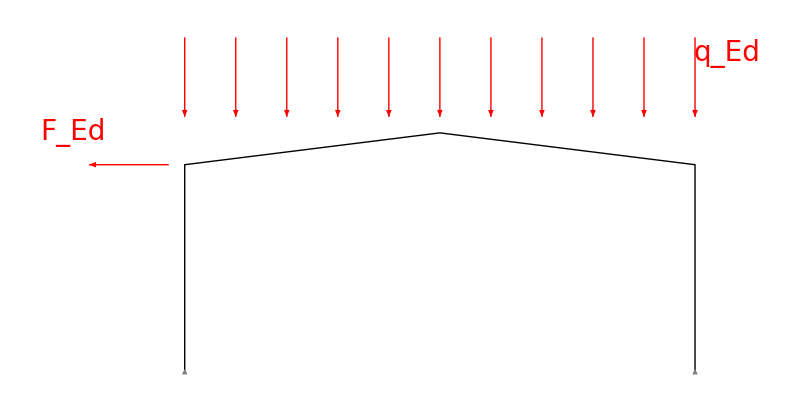

```mathematica
apph=Graphics[{Gray,Triangle[{{-0.5,-1},{0,0},{0.5,-1}}]}];
incv=Graphics[{Gray,Rectangle[{-0.5,-0.5},{0,0.5}]}];
carrh = Graphics[{
Gray,Triangle[{{-0.5,-1},{0,0},{0.5,-1}}],
Gray, Rectangle[{-.5,-1.3}, {.5, -1.8}],
Gray, Circle[{-.2,-1.15},.15],
Gray, Circle[{.2,-1.15},.15]
}];
L=16;h1=6.5;h2=7.5;
portale = {Graphics[{Thick,Line[{{0,0}, {0, h1}, {L/2, h2}, {L, h1}, {L,0}}]}],
Graphics[{Inset[apph, {L,0},{0,0}, Scaled[.1]]}],
Graphics[{Inset[apph, {0,0}, {0,0}, Scaled[.1]]}],
Graphics[{Red,Arrowheads[.02],Table[Arrow[{{i,h2+3},{i,h2+.5}}],{i,0,L,L/10}]}],
Graphics[Text[Style["q_Ed",Italic,Red,28],{L+1,h2+2.5}]],
Graphics[{Red, Arrowheads[.02], Arrow[{{-.5, h1}, {-3, h1}}]}],
Graphics[{Text[Style["F_Ed",Italic, Red, 28], {-3.5, h1+1}]}] 
};
Show[portale, ImageSize->800]
```

```mathematica
1.744
```

1.744

## Analisi dei carichi

## IPE O 360 (classe 1 a flessione, classe 4 a compressione)

```mathematica
Gktrave = 66*9.81/10^3
```

0.64746

## Combinazioni delle azioni

## SLU

```mathematica
dinfluenza = 6.5;
```

### Combo 1: neve principale

```mathematica
{qEd1, qEd1y, qEd1z} = {
1.3*Gktrave + 1.5*qpannCop*dinfluenza+1.5*qsk*Cos[α]*dinfluenza-0*.6*(qwkcop*dinfluenza)/Cos[α]+1.5*0*qcatH,
(1.3*Gktrave + 1.5*qpannCop*dinfluenza+1.5*qsk*Cos[α]*dinfluenza-0*.6*(qwkcop*dinfluenza)/Cos[α]+1.5*0*qcatH)*Cos[α],
(1.3*Gktrave + 1.5*qpannCop*dinfluenza+1.5*qsk*Cos[α]*dinfluenza-0+1.5*0*qcatH)*Sin[α]
}
```

{17.3447,17.2107,2.15134}

La forza concentrata degli arcarecci sul portale

```mathematica
FarcEd1  = 1.5*Garc*dinfluenza/2*10^3
```

899.087

Forza del vento laterale

```mathematica
FwEd1= 1.5*0.6*qwklat*6.5*6.5*10^3
```

23195.2

#### Azioni interne

-Graphics-

-Graphics-

-Graphics-

### Combo 2: vento principale favorevole

```mathematica
{qEd2, qEd2y, qEd2z} = {
1.*Gktrave + .8*qpannCop*dinfluenza-1.5*qwkcop/Cos[α]*dinfluenza+0*0.5*qsk*Cos[α]*dinfluenza+0*0*qcatH,
(1.*Gktrave + .8*qpannCop*dinfluenza-1.5*qwkcop/Cos[α]*dinfluenza+0*0.5*qsk*Cos[α]*dinfluenza+0*0*qcatH)*Cos[α],
(1.*Gktrave + .8*qpannCop*dinfluenza-1.5*0*dinfluenza+0*0.5*qsk*Cos[α]*dinfluenza+0*0*qcatH)*Sin[α]
}
```

{-7.25697,-7.20093,0.148009}

La forza concentrata degli arcarecci sul portale

```mathematica
FarcEd2 = .8*Garc*dinfluenza/2*10^3
```

479.513

Forza del vento laterale

```mathematica
FwEd2 = 1.5*qwklat*6.5*6.5*10^3
```

38658.8

#### Azioni interne

-Graphics-

-Graphics-

-Graphics-

### Combo 3: Cat. H principale

```mathematica
{qEd3, qEd3y, qEd3z} = {
1.3*Gktrave + 1.5*qpannCop*dinfluenza+1.5*.5*qsk*Cos[α]*dinfluenza-0*.6*(qwkcop*dinfluenza)/Cos[α]+1.5*qcatH,
(1.3*Gktrave + 1.5*qpannCop*dinfluenza+1.5*.5*qsk*Cos[α]*dinfluenza-0*.6*(qwkcop*dinfluenza)/Cos[α]+1.5*qcatH)*Cos[α],
(1.3*Gktrave + 1.5*qpannCop*dinfluenza+1.5*.5*qsk*Cos[α]*dinfluenza-0+1.5*qcatH)*Sin[α]
}
```

{10.3549,10.2749,1.28437}

La forza concentrata degli arcarecci sul portale

```mathematica
FarcEd3  = 1.5*Garc*dinfluenza/2*10^3
```

899.087

Forza del vento laterale

```mathematica
FwEd3= 1.5*0.6*qwklat*6.5*6.5*10^3
```

23195.2

#### Azioni interne

-Graphics-

-Graphics-

-Graphics-

## SLE Rara

```mathematica
dinfluenza = 6.5;
```

### Combo 1: neve principale

```mathematica
{qEd1rara, qEd1yrara, qEd1zrara} = {
Gktrave + qpannCop*dinfluenza+qsk*Cos[α]*dinfluenza-.6*(qwkcop*dinfluenza)/Cos[α]+0*qcatH,
(Gktrave + qpannCop*dinfluenza+qsk*Cos[α]*dinfluenza-.6*(qwkcop*dinfluenza)/Cos[α]+0*qcatH)*Cos[α],
(Gktrave + qpannCop*dinfluenza+qsk*Cos[α]*dinfluenza+0+0*qcatH)*Sin[α]
}
```

{8.26933,8.20548,1.44493}

La forza concentrata degli arcarecci sul portale

```mathematica
FarcEd1rara  = Garc*dinfluenza/2*10^3
```

599.391

Forza del vento laterale

```mathematica
FwEd1rara= 0.6*qwklat*6.5*6.5*10^3
```

15463.5

#### Azioni interne

-Graphics-

-Graphics-

-Graphics-

### Combo 2: vento principale favorevole

```mathematica
{qEd2rara, qEd2yrara, qEd2zrara} = {
Gktrave + qpannCop*dinfluenza-qwkcop/Cos[α]*dinfluenza+0.5*qsk*Cos[α]*dinfluenza+0*qcatH,
(Gktrave + qpannCop*dinfluenza-qwkcop/Cos[α]*dinfluenza+0.5*qsk*Cos[α]*dinfluenza+0*qcatH)*Cos[α],
(Gktrave + qpannCop*dinfluenza-0+0.5*qsk*Cos[α]*dinfluenza+0*qcatH)*Sin[α]
}
```

{0.856088,0.849477,0.804935}

La forza concentrata degli arcarecci sul portale

```mathematica
FarcEd2rara= Garc*dinfluenza/2*10^3
```

599.391

Forza del vento laterale

```mathematica
FwEd2rara= qwklat*6.5*6.5*10^3
```

25772.5

#### Azioni interne

-Graphics-

-Graphics-

-Graphics-

### Verifica sugli spostamenti

In combinazione 1 con neve principale l’abbassamento massimo del colmo con la configurazione HE 240 B e IPE O 360 è di 78 mm. La normativa impone che lo spostamento verticale massimo per coperture deve essere limitato a L/200 = (16000mm)/200 = 80mm. La verifica è superata.

## Elementi del portale - caratteristiche geometriche e meccaniche

```mathematica
ClearAll[Jyc, Jzc,Jyt,Jzt, Ac, At, fy, Wplyc, Wplzc, Wplyt, Wplzt, ht, hc, bt, bc, Welyt, Welzt, Welyc, Welzc, Avzt, Avzc, twt, twc, tft, tfc, rt,rc, dt, dc];
fy = 355;
Es = 210*10^3;

(*IPE O 360 - classe 1 a flessione, classe 3 a compressione*)

Lt = 8/Cos[α]*10^3;

Jyt = 19040*10^4;
Jzt = 1251*10^4;
Jtt = 55.74*10^6;
Jωt = 380.2*10^9;
At = 84.1*10^2;
ht = 364;
bt = 172;
Welyt = 1046*10^3;
Wplyt = 1186*10^3;
Welzt = 145.4*10^3;
Wplzt = 226.9*10^3;
Avzt = 40.20*10^2;
twt = 9.2;
tft = 14.7;
rt = 18;
dt = 298.6;

(*HE 240 B -  classe 1 a flessione e compressione*)

Lc = 6500;

Jyc = 11250*10^4;
Jzc = 3922*10^4;
Jtc = 103.8*10^6;
Jωc = 486.9*10^9;
Ac = 106*10^2;
hc = 240;
bc = 240;
Welyc = 938.2*10^3;
Wplyc = 1053*10^3;
Welzc = 326.8*10^3;
Wplzc = 498.4*10^3;
Avzc = 33.22*10^2;
twc = 10;
tfc = 17;
rc = 21;
dc = 164;

ClearAll[MEdSLU, NEdtSLU, NEdcSLU, VEdtSLU, VEdcSLU]
MEdSLU = 340*10^6; (*N mm*)
NEdtSLU = 48*10^3; (*N di compressione sulla trave*)
NEdcSLU = 154*10^3; (*N di compressione sulla colonna*)
VEdtSLU = 148*10^3; (*N sulla trave*)
VEdcSLU = 53*10^3; (*N*)
```

## Imperfezioni globali sul portale

### Sway

```mathematica
ClearAll[ϕ0, αh, αm, ϕ, hpiano, HEd];
hpiano = 7.5;(*m*)
ϕ0 = 1/200;
αh = Min[Max[2/Sqrt[hpiano], 2/3], 1]
αm = Sqrt[.5*(1+1/2)]
ϕ = ϕ0*αh*αm
HEd = NEdcSLU*ϕ
```

0.730297

0.866025

0.00316228

486.991

L’imperfezione può essere trascurata se H_Ed ≥ 0.15 V_Ed

```mathematica
If[FwEd1 >= .15*(qEd1*Lt + 9/2*FarcEd1), TextCell["L'imperfezione di Sway può essere trascurata", "Section"], TextCell["L'imperfezione di Sway NON può essere trascurata", "Section"]]
```

L'imperfezione di Sway può essere trascurata

### Curvatura iniziale

L’imperfezione di curvatura iniziale dell’elemento deve essere considerata anche nell’analisi globale se
											
											è uno dei nodi estremi è a momento resistente (non è una cerniera)
														
														e

											λ = √((A f_y)/N_cr) > 0.5 √((A f_y)/N_Ed)
dove λ è la snellezza adimensionale considerando l’elemento incernierato agli estremi. N_cr vale allora

												N_cr= π^2* EJ/L^2

```mathematica
Ncr[Ee_, J_, L0_]:= π^2*Ee*J/L0^2
λ[A_, fy_, Ncr_]:= √((A*fy)/Ncr)
If[λ[At, fy, Ncr[Es, Min[Jyt, Jzt], Lt]] > .5*√(At*fy/NEdtSLU), TextCell["Si deve considerare l'imperfezione di curvatura iniziale nell'analisi globale", "Section"] , TextCell["Non è necessario considerare l'imperfezione di curvatura iniziale nell'analisi globale", "Section"]]
```

Non è necessario considerare l'imperfezione di curvatura iniziale nell'analisi globale

## Calcolo di α_cr

Il calcolo di α_cr in modo approssimato può essere condotto come segue, se la snellezza adimensionale della trave nel piano (x-y) è limitata a

										λ < .3 √((A f_y)/N_Ed)
In prima approssimazione si può considerare 

L_(0,T) = L_T

```mathematica
{λyt, λzt} = {λ[At, fy, Ncr[Es, Jyt, Lt]], λ[At, fy, Ncr[Es, Jzt, Lt]]}
 If[λyt <.3*√((At*fy)/NEdtSLU), TextCell["E' possibile calcolare alpha critico in modo approssimato", "Section"], TextCell["Non è possibile calcolare alpha critico in modo approssimato", "Section"]]
```

{0.701255,2.73578}

E' possibile calcolare alpha critico in modo approssimato

### Combo 1

```mathematica
Hpiano1 = FwEd1
Vpiano1 =Round[qEd1*2*Lt+9*FarcEd1, .1]
```

23195.2

287766.

Lo spostamento del piano dovuto alle sole azioni orizzontali (SLU Combo 1) è di 78 mm

```mathematica
δHEd1= 0.078*10^3; (*mm*)
αcr1 = (Hpiano1/Vpiano1)*((hpiano*10^3)/δHEd1)
If[αcr1 > 10, TextCell["L'analisi al II ordine non è necessaria", "Section"], TextCell["L'analisi al II ordine è necessaria!", "Section"]]
```

7.75044

L'analisi al II ordine è necessaria!

```mathematica
Hpiano2 = FwEd2
Vpiano2 =qEd2*2*Lt+9*FarcEd2
```

38658.8

-112699.

Lo spostamento del piano dovuto alle sole azioni orizzontali (SLU Combo 2) è di 13.04 cm

```mathematica
δHEd2 = 0.1304*10^3; (*mm*)
αcr2 = Abs[(Hpiano2/Vpiano2)*((hpiano*10^3)/δHEd2)]
If[αcr2 > 10, TextCell["L'analisi al II ordine non è necessaria", "Section"], TextCell["L'analisi al II ordine è necessaria!", "Section"]]
```

19.7292

L'analisi al II ordine non è necessaria

Essendo α_cr< 10 per la combo 1, è comunque necessario fare l’analisi del II ordine!

```mathematica
Hpiano3 = FwEd3
Vpiano3 =qEd3*2*Lt+9*FarcEd3
```

23195.2

175059.

Lo spostamento del piano dovuto alle sole azioni orizzontali (SLU + imperfezioni) è di 78 mm

```mathematica
δHEd3= 0.078*10^3; (*mm*)
αcr3 = (Hpiano3/Vpiano3)*((hpiano*10^3)/δHEd3)
If[αcr3 > 10, TextCell["L'analisi al II ordine non è necessaria", "Section"], TextCell["L'analisi al II ordine è necessaria!", "Section"]]
```

12.7403

L'analisi al II ordine non è necessaria

Infine:

```mathematica
If[αcr1 > 10 Or αcr2 > 10 Or αcr3 > 10 , TextCell["L'analisi al II ordine non è necessaria", "Section"], TextCell["L'analisi al II ordine è necessaria!", "Section"]]
```

L'analisi al II ordine è necessaria!

## Effetti del II ordine

Per portali a un piano, gli effetti del II ordine possono essere considerati andando ad aumentare l’azione orizzontale agente sul portale del fattore
	
									1/(1-1/α_cr), 	α_cr ≥ 3
per ogni combinazione di carico!

## Combo 1:

```mathematica
Hpiano1
HEdtot1 = Hpiano1*1/(1-1/Max[αcr1, 3])
```

23195.2

26631.4

## Combo 2:

```mathematica
Hpiano2
HEdtot2 = Hpiano2*1/(1-1/Max[αcr2, 3])
```

38658.8

40722.8

## Combo 3:

```mathematica
Hpiano3
HEdtot3 = Hpiano3*1/(1-1/Max[αcr3, 3])
```

23195.2

25170.9

## Sollecitazioni del II ordine

Le azioni interne che si sviluppano con la configurazione che tiene conto degli effetti del secondo ordine sono

```mathematica
qEd3y
```

10.2749

## Combo 1:

Il momento al colmo vale 281 kNm (tende le fibre inferiori).
Il momento massimo agente sul traverso sinistro vale 350 kNm (tende le fibre superiori), mentre sul traverso destro il massimo momento vale 281 kNm sul colmo (176 kNm sul nodo con la colonna destra).

L’azione assiale al colmo vale 28.2 kN di compressione.

Il taglio al colmo vale 8 kN.

```mathematica
MEdtglob1 = 350*10^6;(*Nmm*)
MEdcglob1 = MEdtglob1; (*Nmm*)

NEdtglob1 = 46*10^3; (*N di compressione*)
NEdcglob1 = 154*10^3; (*N di compressione*)

VEdtglob1 = 150*10^3;
VEdcglob1 = 54*10^3;
```

## Combo 2:

Il momento al colmo vale -92 kNm (tende le fibre superiori).
Il momento massimo agente sul traverso sinistro vale -124 kNm (tende le fibre superiori), mentre sul traverso destro il massimo momento vale 224 kNm sul nodo trave-colonna.

L’azione assiale al colmo vale 36.17 kN di trazione a destra e 32.1 kN di trazione a sinistra.

Il taglio al colmo vale 21.2 kN a sinistra e 12 kN a destra.
Il taglio massimo sul traverso di sinistra vale 34 kN, e sul traverso di destra vale 67 kN.
Il taglio sulla colonna di sinistra vale 6.3 kN, mentre sulla colonna di destra vale 34.5 kN.

```mathematica
MEdtglob2 = 224*10^6;(*Nmm tende le fibre all'intradosso nel nodo trave-colonna di destra*)
MEdcglob2 = MEdtglob2; (*Nmm*)

NEdtglob2 = 43*10^3; (*N di trazione*)
NEdcglob2 = 71*10^3; (*N di trazione*)

VEdtglob2 = 67*10^3;
VEdcglob2 = 34.5*10^3;
```

## Combo 3:

Il momento al colmo vale 173.3 kNm (tende le fibre inferiori).
Il momento massimo agente sul traverso sinistro vale - 243 kNm (tende le fibre superiori), mentre sul traverso destro il massimo momento vale 173.3 kNm sul colmo.
Sul nodo trave colonna destro il momento vale -78.7 kNm tendente le fibre all’estradosso del traverso.

L’azione assiale al colmo vale 13.33 kN di compressione a sinistra e 10.8 kN di compressione a destra.

Il taglio al colmo vale 9.1 kN a sinistra e 11.2 kN a destra.
Il taglio massimo sul traverso di sinistra vale 95 kN, e sul traverso di destra vale 74 kN.
Il taglio sulla colonna di sinistra vale 38 kN, mentre sulla colonna di destra vale 12.1 kN.

```mathematica
MEdtglob3 = 243*10^6;(*Nmm*)
MEdcglob3 = MEdtglob3; (*Nmm*)

NEdtglob3 = 24*10^3; (*N di compressione*)
NEdcglob3 = 98*10^3; (*N di compressione*)

VEdtglob3 = 95*10^3;
VEdcglob3 = 38*10^3;
```

## Sollecitazioni di progetto

Le sollecitazioni di progetto sono il massimo tra le sollecitazioni agenti nelle 3 combinazioni

```mathematica
MEdtglob = Max[MEdtglob1, MEdtglob2, MEdtglob3]
MEdcglob = Max[MEdcglob1, MEdcglob2, MEdcglob3]
NEdtglob = Max[NEdtglob1, NEdtglob2, NEdtglob3]
NEdcglob = Max[NEdcglob1, NEdcglob2, NEdcglob3]
VEdtglob = Max[VEdtglob1, VEdtglob2, VEdtglob3]
VEdcglob = Max[VEdcglob1, VEdcglob2, VEdcglob3]
```

350000000

350000000

46000

154000

150000

54000

## Verifiche di resistenza delle sezioni

```mathematica
MplRdyt> MEdglob
MplRdyc > MEdglob
NRdt > NEdtglob
NRdc > NEdcglob

MEdglob/Wplyt- NEdtglob/At< fy/1.05
NEdcglob ≤ .25*NplRdc
NEdcglob ≤ (.5*twc*dc*fy)/1.05
NEdcglob ≤ (twc*dc*fy)/1.05
```

True

True

True

«5 more identical outputs»

La colonna HE 240 B è sufficiente!

## Verifiche di resistenza per gli elementi del portale

## Compressione

### Traverso IPE O 360

In prima approssimazione si sceglie L_(0,T) = L_T = 8.06 m

```mathematica
L0t = Lt;
Ncr[EJ_, l0_]:=(π^2*EJ)/l0^2
NplRdt = NplRd[At, fy]
{Ncryt,Ncrzt }= {Ncr[Es*Jyt, L0t], Ncr[Es*Jzt, L0t]}
{λyt, λzt} = {Sqrt[At*fy/Ncryt], Sqrt[At*fy/Ncrzt]}
αyt = If[ht/bt≤1.2, .34, .21]
αzt = If[ht/bt≤1.2, .49, .34]
{ϕyt, ϕzt} = .5*(1+{αyt, αzt}*({λyt, λzt}-.2)+({λyt, λzt})^2)
{χyt, χzt} = 1/({ϕyt, ϕzt}+Sqrt[({ϕyt, ϕzt})^2-({λyt, λzt})^2])
{NbRdyt, NbRdzt} = {χyt, χzt} *(At*fy)/1.05
If[NEdtglob≤ Min[NplRdt,NbRdyt, NbRdzt], TextCell["Verificato!", "Section"]]
```

2.84338×10^6

{6.07117×10^6,398899.}

{0.701255,2.73578}

0.21

0.34

{0.798511,4.67332}

{0.84715,0.118173}

{2.40877×10^6,336011.}

Verificato!

### Colonna HE 240 B

In prima approssimazione si sceglie L_(0,c) = L_c = 6.50m

```mathematica
L0c = Lc;
Ncr[EJ_, l0_]:=(π^2*EJ)/l0^2
NplRdc = NplRd[Ac, fy]
{Ncryc,Ncrzc }= {Ncr[Es*Jyc, L0c], Ncr[Es*Jzc, L0c]}//N
{λyc, λzc} = {Sqrt[Ac*fy/Ncryc], Sqrt[Ac*fy/Ncrzc]}
αyc = If[hc/bc≤1.2, .34, .21]
αzc = If[hc/bc≤1.2, .49, .34]
{ϕyc, ϕzc} = .5*(1+{αyc, αzc}*({λyc, λzc}-.2)+({λyc, λzc})^2)
{χyc, χzc} = 1/({ϕyc, ϕzc}+Sqrt[({ϕyc, ϕzc})^2-({λyc, λzc})^2])
{NbRdyc, NbRdzc} = {χyc, χzc} *(Ac*fy)/1.05
{NEdcglob/NbRdyc, NEdcglob/NbRdzc}
If[NEdcglob≤ Min[NplRdc,NbRdyc, NbRdzc], TextCell["Verificato!", "Section"]]
```

3.58381×10^6

{5.5188×10^6,1.92398×10^6}

{0.825743,1.39852}

0.34

0.49

{0.947302,1.77156}

{0.708439,0.34977}

{2.53891×10^6,1.25351×10^6}

{0.0606559,0.122855}

Verificato!

## Flessione

### Traverso IPE O 360

```mathematica
{MplRdyt, MplRdzt} = {Mpl[Wplyt,fy], Mpl[Wplzt,fy]}
If[MEdtglob≤ MplRdyt , TextCell["Verificato!", "Section"], TextCell["Non verificato!", "Section"]]
```

{4.00981×10^8,7.67138×10^7}

Verificato!

### Colonna HE 240 B

```mathematica
{MplRdyc, MplRdzc} = {Mpl[Wplyc,fy], Mpl[Wplzc,fy]}
If[MEdcglob≤ MplRdyc , TextCell["Verificato!", "Section"], TextCell["Non verificato!", "Section"]]
```

{3.56014×10^8,1.68507×10^8}

Verificato!

## Taglio

### Traverso IPE O 360

```mathematica
VcRdt = Vpl[Avzt, fy]
If[VcRdt≥ VEdtglob, TextCell["Verificato!", "Section"]]
If[VEdtglob < .5*VcRdt, TextCell["Effetto del taglio trascurabile!", "Section"], TextCell["Effetto del taglio NON trascurabile!", "Section"]]
```

784701.

Verificato!

Effetto del taglio trascurabile!

Poiché V_Ed< 0.5 V_(c,Rd) allora è sufficiente la verifica a presso-flessione, senza contare il contributo del taglio (p.to 6.2.8 (2) EC3)

### Colonna HE 240 B

```mathematica
VcRdc= Vpl[Avzc, fy]
If[VcRdc≥ VEdcglob, TextCell["Verificato!", "Section"], TextCell["Non verificato!", "Section"]]
If[VEdcglob < .5*VcRdc, TextCell["Effetto del taglio trascurabile!", "Section"], TextCell["Effetto del taglio NON trascurabile!", "Section"]]
```

648452.

Verificato!

Effetto del taglio trascurabile!

Poiché V_Ed< 0.5 V_(c,Rd) allora è sufficiente la verifica a presso-flessione, senza contare il contributo del taglio (p.to 6.2.8 (2) EC3)

## Presso-flessione

### Traverso IPE O 360

```mathematica
If[NEdtglob ≤ .25 NplRdt && NEdtglob ≤ (0.5*dt*twt)/1.05*fy && NEdtglob ≤ (dt*twt)/1.05*fy, TextCell["Effetto dell'azione assiale trascurabile", "Section"], TextCell["Effetto dell'azione assiale NON trascurabile", "Section"]]
```

Effetto dell'azione assiale trascurabile

L’azione assiale non ha effetti significativi!

Si può comunque fare la verifica:

```mathematica
at = Min[(At-2*bt*tft)/At, .5];
MNRdyt = Min[MplRdyt*(1-NEdtglob/NplRdt)/(1-.5*at), MplRdyt]
MNRdzt = If[NEdtglob/NplRdt≤ at, MplRdzt, MplRdzt*(1-((NEdtglob/NplRdt-at)/(1-at))^2)]
If[(MEdtglob/MNRdyt)^2+ 0≤1, TextCell["Verificato!", "Section"]]
```

4.00981×10^8

7.67138×10^7

Verificato!

### Colonna HE 240 B

```mathematica
If[NEdcglob ≤ .25 NplRdc && NEdcglob ≤ (0.5*dc*twc)/1.05*fy && NEdcglob ≤ (dc*twc)/1.05*fy, TextCell["Effetto dell'azione assiale trascurabile", "Section"], TextCell["Effetto dell'azione assiale NON trascurabile", "Section"]]
```

Effetto dell'azione assiale trascurabile

L’azione assiale non ha effetti significativi!

Si può comunque fare la verifica:

```mathematica
ac = Min[(Ac-2*bc*tfc)/Ac, .5];
MNRdyc = Min[MplRdyc*(1-NEdcglob/NplRdc)/(1-.5*ac), MplRdyc]
MNRdzc = If[NEdcglob/NplRdc≤ ac, MplRdzc, MplRdzc*(1-((NEdcglob/NplRdc-ac)/(1-ac))^2)]
If[(MEdcglob/MNRdyc)^2+ 0≤1, TextCell["Verificato!", "Section"]]
```

3.56014×10^8

1.68507×10^8

Verificato!

## Verifiche di stabilità per gli elementi del portale: traverso con ritegni laterali (arcarecci) e colonna

## Combo 1:

-Graphics-

Nella zona in cui il momento tende le fibre inferiori la flangia compressa è la quella superiore che però è stabilizzata dalla presenza degli arcarecci che sono connessi ad essa. La lunghezza di libera inflessione da considerare è allora l’interasse tra gli arcarecci

						L_(0pos) = 2.02 m
						
Nella zona in cui il momento flettente è negativo la flangia compressa è quella inferiore che non è stabilizzata. La lunghezza da considerare nell’analisi è la distanza tra il momento massimo negativo e il momento nullo. Supponendo in questa zona il diagramma di tipo lineare

```mathematica
L0tpos = iarc*10^3
L0tneg = x/.Solve[(x-0)/(2.02*10^3-0)== (0+348.3*10^6)/(-84.33*10^6+348.3*10^6), x][[1]]
```

2020.

2665.33

## Instabilità latero-torsionale

### Traverso IPE O 360 - momento positivo

#### Calcolo del momento critico

N_(cr,T) = A/(J_y+J_z)[G J_t + (π^2 E J_ω)/L^2]

Il momento critico che non tiene conto dello sforzo assiale (N_Ed=0) è [kN m]
M_cr=C_1[π/L √(G J_t E J_z(1+(π^2 E J_ω)/(L^2 G J_t)))]

Il momento critico elastico per instabilità L-T, che tiene conto dello sforzo assiale di compressione è
M_(cr,N)=C_1[π/L √(G J_t E J_z(1+(π^2 E J_ω)/(L^2 G J_t)))]√((1-N_Ed/(N_(cr,z)))(1-N_Ed/(N_(cr,T))))

```mathematica
Ncrztpos = Ncr[Es, Jzt, L0tpos];

NcrT[A_, Jy_, Jz_, G_, Jt_, Ee_, Jω_, L_]:=A/(Jy+Jz)*(G*Jt+(π^2*Ee*Jω)/L^2)
NcrTtpos = NcrT[At,Jyt,Jzt,Gs,Jtt , Es,Jωt, L0tpos]

McrLT[C1_, L_, G_, Jt_, Ee_, Jz_, Jω_]:=C1*(π/L*Sqrt[G*Jt*Ee*Jz*(1+(π^2*Ee*Jω)/(L^2*G*Jt))]) (*Subscript[N, Ed]=0*)

McrN[C1_, L_, G_, Jt_, Ee_, Jz_, Jω_, NEd_, Ncrz_, NcrT_]:=C1*(π/L*Sqrt[G*Jt*Ee*Jz*(1+(π^2*Ee*Jω)/(L^2*G*Jt))])*Sqrt[(1-NEd/Ncrz)*(1-NEd/NcrT)] (*Subscript[N, Ed]≠ 0*)
(*
Si suppone un andamento del momento di tipo lineasre con ψ=0. Si ricava C1 dal prospetto F.1.1 delle ENV 1993-1-1
*)
C1tpos = 1.879;
McrNtpos = McrN[C1tpos, L0tpos, Gs, Jtt , Es, Jzt, Jωt, NEdtglob, Ncrztpos, NcrTtpos]

(*Snellezza adimensionale, dove Subscript[W, y] =Subscript[W, pl,y]*)
λLT[Wy_, fy_, Mcr_] := Sqrt[(Wy*fy)/Mcr]
λLTtpos = λLT[Wplyt, fy, McrNtpos]
```

1.94602×10^8

1.0225×10^10

0.20292

L’instabilità latero-torsionale può essere ignorata se
λ_LT≤ λ_(LT,0)
o
M_Ed/M_cr≤ (λ_(LT,0))^2

dove, in questo caso, M_Ed è quello massimo al colmo e vale 281 kNm

```mathematica
MEdtcolmo = 281*10^6;
If[λLTtpos ≤ .4 && MEdtcolmo/McrNtpos≤ (.4)^2, TextCell["Non è necessario fare la verifica per LTB", "Section"],  TextCell["E' necessario fare la verifica per LTB", "Section"]]
```

Non è necessario fare la verifica per LTB

### Traverso IPE O 360 - momento negativo

#### Calcolo del momento critico

N_(cr,T) = A/(J_y+J_z)[G J_t + (π^2 E J_ω)/L^2]

Dal software agli EF LTBeamN il valore che si ricava è
M_(max,cr) = 41.79 kN m
Il momento critico che non tiene conto dello sforzo assiale (N_Ed=0) è [kN m]
M_cr=[π/L √(G J_t E J_z(1+(π^2 E J_ω)/(L^2 G J_t)))]

Il momento critico elastico per instabilità L-T, che tiene conto dello sforzo assiale di compressione è
M_(cr,N)=[π/L √(G J_t E J_z(1+(π^2 E J_ω)/(L^2 G J_t)))]√((1-N_Ed/(N_(cr,z)))(1-N_Ed/(N_(cr,T))))

```mathematica
Ncrztneg = Ncr[Es, Jzt, L0tneg];
NcrT[A_, Jy_, Jz_, G_, Jt_, Ee_, Jω_, L_]:=A/(Jy+Jz)*(G*Jt+(π^2*Ee*Jω)/L^2)
NcrTtneg = NcrT[At,Jyt,Jzt,Gs,Jtt , Es,Jωt, L0tneg]

McrLT[C1_, L_, G_, Jt_, Ee_, Jz_, Jω_]:=C1*(π/L*Sqrt[G*Jt*Ee*Jz*(1+(π^2*Ee*Jω)/(L^2*G*Jt))]) (*Subscript[N, Ed]=0*)

McrN[C1_, L_, G_, Jt_, Ee_, Jz_, Jω_, NEd_, Ncrz_, NcrT_]:=C1*(π/L*Sqrt[G*Jt*Ee*Jz*(1+(π^2*Ee*Jω)/(L^2*G*Jt))])*Sqrt[(1-NEd/Ncrz)*(1-NEd/NcrT)] (*Subscript[N, Ed]≠ 0*)
(*
Dal prospetto F.1.1 della ENV 1993-1-1 si ricava il valore di C1 per ψ=0 e kz=kω=1
*)
C1tneg = 1.879; 

McrNtneg = McrN[C1tneg, L0tneg, Gs, Jtt , Es, Jzt, Jωt, NEdtglob, Ncrztneg, NcrTtneg]

(*Snellezza adimensionale, dove Subscript[W, y] =Subscript[W, pl,y]*)
λLT[Wy_, fy_, Mcr_] := Sqrt[(Wy*fy)/Mcr]
λLTtneg = λLT[Wplyt, fy, McrNtneg]
```

1.91195×10^8

7.66038×10^9

0.23444

L’instabilità latero-torsionale può essere ignorata se
λ_LT≤ λ_(LT,0)
o
M_Ed/M_cr≤ (λ_(LT,0))^2

```mathematica
If[λLTtneg ≤ .4 && MEdtglob/McrNtpos≤ (.4)^2, TextCell["Non è necessario fare la verifica per LTB", "Section"],  TextCell["E' necessario fare la verifica per LTB", "Section"]]
```

Non è necessario fare la verifica per LTB

### Colonna HE 240 B

#### Calcolo del momento critico

N_(cr,T) = A/(J_y+J_z)[G J_t + (π^2 E J_ω)/L^2]

Il momento critico che non tiene conto dello sforzo assiale (N_Ed=0) è [kN m]
M_cr=C_1[π/L √(G J_t E J_z(1+(π^2 E J_ω)/(L^2 G J_t)))]

Il momento critico elastico per instabilità L-T, che tiene conto dello sforzo assiale di compressione è
M_(cr,N)=C_1[π/L √(G J_t E J_z(1+(π^2 E J_ω)/(L^2 G J_t)))]√((1-N_Ed/(N_(cr,z)))(1-N_Ed/(N_(cr,T))))

```mathematica
L0c = Lc;
Ncrzc = Ncr[Es, Jzc, L0c]//N
NcrT[A_, Jy_, Jz_, G_, Jt_, Ee_, Jω_, L_]:=A/(Jy+Jz)*(G*Jt+(π^2*Ee*Jω)/L^2)
NcrTc = NcrT[Ac,Jyc,Jzc,Gs,Jtc , Es,Jωc, L0c]

McrLT[C1_, L_, G_, Jt_, Ee_, Jz_, Jω_]:=C1*(π/L*Sqrt[G*Jt*Ee*Jz*(1+(π^2*Ee*Jω)/(L^2*G*Jt))]) (*Subscript[N, Ed]=0*)

McrN[C1_, L_, G_, Jt_, Ee_, Jz_, Jω_, NEd_, Ncrz_, NcrT_]:=C1*(π/L*Sqrt[G*Jt*Ee*Jz*(1+(π^2*Ee*Jω)/(L^2*G*Jt))])*Sqrt[(1-NEd/Ncrz)*(1-NEd/NcrT)] (*Subscript[N, Ed]≠ 0*)

C1c = 1.879;

McrNc = McrN[C1c, L0c, Gs, Jtc , Es, Jzc, Jωc, NEdcglob, Ncrzc, NcrTc]

(*Snellezza adimensionale, dove Subscript[W, y] =Subscript[W, pl,y]*)
λLT[Wy_, fy_, Mcr_] := Sqrt[(Wy*fy)/Mcr]
λLTc = λLT[Wplyc, fy, McrNc]
```

1.92398×10^6

5.87411×10^8

7.24758×10^9

0.227108

L’instabilità latero-torsionale può essere ignorata se
λ_LT≤ λ_(LT,0)
o
M_Ed/M_cr≤ (λ_(LT,0))^2

```mathematica
If[λLTc ≤ .4 && MEdcglob/McrNc≤ (.4)^2, TextCell["Non è necessario fare la verifica per LTB", "Section"],  TextCell["E' necessario fare la verifica per LTB", "Section"]]
```

Non è necessario fare la verifica per LTB

## Buckling presso-flessione

### Traverso IPE O 360 - momento positivo

```mathematica
ClearAll[ χ, ϕ, λ,A, EJ, l0, NbRd];
χ[ϕ_, λ_] := Min[1/(ϕ+Sqrt[ϕ^2-λ^2]), 1]
ϕ[α_, λ_]:= .5*(1+α*(λ-.2)+λ^2)
λ[A_, fy_, Ncr_]:=Sqrt[A*fy/Ncr]
NbRd[χ_, A_,fy_]:= χ*(A*fy)/1.05

(*Subscript[L, 0z] = Subscript[L, t,pos]= 2.02 m*)
{Ncryt, Ncrzt} ={Ncr[Es, Jyt, L0t],Ncr[Es, Jzt, L0tpos]}

{αyt, αzt} = If[ht/bt≤1.2 , {.34, .49}, {.21, .34}]
{λyt, λzt} = {λ[At, fy, Ncryt], λ[At, fy, Ncrzt]}
{ϕyt, ϕzt} = {ϕ[αyt, λyt], ϕ[αzt, λzt]}
{χyt, χzt} = {χ[ϕyt, λyt], χ[ϕzt, λzt]}
{NbRdyt, NbRdzt} = {NbRd[χyt, At,fy],NbRd[χzt,At,fy]} (*Valore in [N]*)
```

{6.07117×10^6,6.35439×10^6}

{0.21,0.34}

{0.701255,0.685449}

{0.798511,0.817447}

{0.84715,0.791864}

{2.40877×10^6,2.25157×10^6}

La verifica è superata se sono soddisfatte le (6.61), (6.62) del EC3:

N_Ed/((χ_y N_Rk)/γ_m1) + k_yy *(M_(y,Ed + ΔM_(y,Ed)))/((χ_LT * M_(y.Rk))/γ_m1) ≤ 1

N_Ed/((χ_z N_Rk)/γ_m1) + k_zy *(M_(y,Ed + ΔM_(y,Ed)))/((χ_LT * M_(y.Rk))/γ_m1) ≤ 1

Usando il Metodo 1:

k_yy= C_my C_mLT *μ_y/(1-N_Ed/(N_(cr,y)))*1/C_yy
k_zy= C_my C_mLT *μ_z/(1-N_Ed/(N_(cr,y)))*1/C_zy*0.6 √(w_y/w_z)
μ_y = (1-N_Ed/(N_(cr,y)))/(1-χ_y*N_Ed/(N_(cr,y)))
μ_z = (1-N_Ed/(N_(cr,z)))/(1-χ_z*N_Ed/(N_(cr,z)))
w_y = min{(W_(pl,y))/(W_(el,y)), 1.5}
w_z = min{(W_(pl,z))/(W_(el,z)), 1.5}
n_pl = N_Ed/(N_Rk/γ_m0)
a_LT = 1-J_T/J_y
C_yy = max{1+(w_y-1)*[(2-1.6/w_y C_my^2 λ_max- 1.6/w_y C_my^2 λ_max^2)*n_pl-b_LT], (W_(el,y))/(W_(pl,y))}
b_LT = 0.5*a_LT λ_0^2*(M_(y,Ed))/(χ_LT M_(pl,y,Rd))*(M_(z,Ed))/(M_(pl,z,Rd))
C_zy = max{1+(w_y-1)*[(2-14 C_my^2 λ_max^2/w_y^5)*n_pl-d_LT], 0.6*√(w_y/w_z)(W_(el,y))/(W_(pl,y))}
d_LT = 2 a_LT*λ_0/(0.1+λ_z^4)*(M_(y,Ed))/(C_my χ_LT M_(pl,y,Rd))*(M_(z,Ed))/(C_mz M_(pl,z,Rd))

λ_max = max{λ_y, λ_z}
λ_0 ∈ [0.2, 0.4]

Se λ_0 ≤ λ_(0,LIM) = 0.2 √C_1*((1-N_Ed/(N_(cr,z)))(1-N_Ed/(N_(cr,T))))^(1/4) le deformazioni torsionali sono trascurabili e C_my = C_(my,0) (vedi Table A.2)
C_1 = k_c^-2 con k_c da Table 6.6

Se λ_0 > λ_(0,LIM) = 0.2 √C_1*((1-N_Ed/(N_(cr,z)))(1-N_Ed/(N_(cr,T))))^(1/4) le deformazioni torsionali non sono trascurabili e:
	C_my = C_(my,0) + (1-C_(my,0))*(√ϵ_y a_LT)/(1+√ϵ_y a_LT)
	C_mz = C_(mz,0)
	C_mLT = max{C_my^2*a_LT/(√((1-N_Ed/(N_(cr,z)))(1-N_Ed/(N_(cr,T))))), 1}
	con ϵ_y = (M_(y,Ed))/N_Ed*A/(W_(el,y)) per sezioni di classe 1,2,3.

```mathematica
(*
----------- HP. ANDAMENTO DEL MOMENTO DI TIPO LINEARE --------------------
kz = 1;
kω = 1;
*)
ψt=0;
If[.2 ≤ .2*√C1tpos*((1-NEdtglob/Ncrzt)*(1-NEdtglob/NcrTtpos))^(1/4), TextCell["Deformazioni torsionali trascurabili\n Cmy = Cmy0\n CmLT = 1", "Subsubsection"], TextCell["Deformazioni torsionali NON trascurabili","Subsubsection"]]
```

Deformazioni torsionali trascurabili
 Cmy = Cmy0
 CmLT = 1

C_(my,0) = 0.79 + 0.21 ψ_y + 0.36*(ψ_y - 0.33) *N_Ed/(N_(cr,y))

```mathematica
ϵy[MEdy_, NEd_, A_, Wely_] := MEdy/NEd*A/Wely (*deformazioni torsionali non trascurabili*)
aLT[Jt_, Jy_] := Max[1-Jt/Jy, 0]
(*Cmy[Cmy0_, ϵy_, aLT_] := Cmy0 + (1-Cmy0)*(√ϵy*aLT)/(1+√ϵy*aLT)  deformazioni torsionali non trascurabili*)
(*CmLT[Cmy_, aLT_, NEd_, Ncrz_, NcrT_] := Max[Cmy^2*aLT/(√((1-NEd/Ncrz)*(1-NEd/NcrT))), 1] deformazioni torsionali non trascurabili*)
w[Wply_, Wely_]:=Min[Wply/Wely, 1.5]
Ncr[EJ_, L0_]:= π^2*EJ/L0^2
λ[A_, fy_, Ncr_]:=√((A*fy)/Ncr)
λmax[λy_, λz_] := Max[λy, λz]
npl[NEd_, NRk_]:= NEd/(NRk/1.05)
bLT[aLT_, λ0_, MyEd_,χLT_, MplyRd_, MzEd_, MplzRd_]:= .5*aLT*λ0^2*MyEd/(χLT * MplyRd)*MzEd/MplzRd
Cyy[wy_, Cmy_, λmax_, npl_, bLT_, Wely_, Wply_]:=Max[1+(wy-1)*((2-1.6/wy*Cmy^2*λmax-1.6/wy*Cmy^2*λmax^2)*npl-bLT), Wely/Wply]
μ[NEd_, Ncr_, χ_]:= (1-NEd/Ncr)/(1-χ*NEd/Ncr)
kyy[Cmy_, CmLT_, μy_, NEd_, Ncry_, Cyy_]:= Cmy*CmLT*μy/(1-NEd/Ncry)*1/Cyy

(*---------------------------*)

Cmy0t=.79+.21*ψt+.36*(ψt-.33)*NEdtglob/Ncryt;
Cmyt = Cmy0t
CmLTt = 1;
aLTt = aLT[Jtt, Jyt];
wyt = w[Wplyt, Welyt]
λmaxt = λmax[λyt, λzt]
nplt = npl[NEdtglob, NplRdt]
χLTt = 1;
MEdztglob = 0;
bLTt = bLT[aLTt, .2, MEdtcolmo, χLTt, MplRdyt, MEdztglob, MplRdzt]
Cyyt = Cyy[wyt, Cmyt, λmaxt, nplt, bLTt, Welyt, Wplyt]
μyt = μ[NEdtglob, Ncryt, χyt]
kyyt = kyy[Cmyt, CmLTt, μyt, NEdtglob,Ncryt, Cyyt]
```

0.7891

593/523

0.701255

0.0169868

0.

1.00216

0.998834

0.792483

Allora la (6.1) del EC3 diventa

```mathematica
If[NEdtglob/(χyt*NplRdt)+kyyt*MEdtcolmo/(χLTt*MplRdyt)≤1, TextCell["Verifica Soddisfatta!", "Section"], TextCell["Verifica NON Soddisfatta!", "Section"]]
```

Verifica Soddisfatta!

```mathematica
dLT[aLT_,λ0_, λz_, MyEd_, Cmy_, χLT_, MplyRd_, MzEd_, Cmz_, MplzRd_]:=2*aLT*λ0/(.1+λz^4)*MyEd/(Cmy*χLT*MplyRd)*MzEd/(Cmz*MplzRd)
Czy[wy_, Cmy_, λmax_, npl_, dLT_, wz_, Wely_, Wply_]:=Max[1+(wy-1)*((2-14*(Cmy^2*λmax^2)/wy^5)*npl - dLT), .6*√(wy/wz)* Wely/Wply]
kzy[Cmy_, CmLT_, μz_, NEd_, Ncry_, Czy_, wy_, wz_]:= Cmy*CmLT*μz/(1-NEd/Ncry)*1/Czy*.6*√(wy/wz)

(*-------------------------*)
wzt = w[Wplzt, Welzt]
μzt = μ[NEdtglob, Ncrzt, χzt]
dLTt = dLT[aLTt, .2, λzt, MEdtcolmo, Cmyt, χLTt, MplRdyt, MEdztglob, 1, MplRdzt]
Czyt = Czy[wyt, Cmyt, λmaxt, nplt, dLTt, wzt, Welyt, Wplyt]
kzyt = kzy[Cmyt, CmLTt, μzt, NEdtglob, Ncryt, Czyt, wyt, wzt]

(*-------------------------*)

If[NEdtglob/(χzt*NplRdt)+kzyt*MEdtcolmo/(χLTt*MplRdyt)≤1, TextCell["Verifica Soddisfatta!", "Section"], TextCell["Verifica NON Soddisfatta!", "Section"]]
```

1.5

0.998485

0.

0.999346

0.414422

Verifica Soddisfatta!

### Traverso IPE O 360 - momento negativo

```mathematica
ClearAll[ χ, ϕ, λ,A, EJ, l0, NbRd];
χ[ϕ_, λ_] := Min[1/(ϕ+Sqrt[ϕ^2-λ^2]), 1]
ϕ[α_, λ_]:= .5*(1+α*(λ-.2)+λ^2)
λ[A_, fy_, Ncr_]:=Sqrt[A*fy/Ncr]
NbRd[χ_, A_,fy_]:= χ*(A*fy)/1.05

(*Subscript[L, 0z] = Subscript[L, t,pos]= 2.02 m*)
{Ncryt, Ncrzt} ={Ncr[Es, Jyt, L0t],Ncr[Es, Jzt, L0tneg]}

{αyt, αzt} = If[ht/bt≤1.2 , {.34, .49}, {.21, .34}]
{λyt, λzt} = {λ[At, fy, Ncryt], λ[At, fy, Ncrzt]}
{ϕyt, ϕzt} = {ϕ[αyt, λyt], ϕ[αzt, λzt]}
{χyt, χzt} = {χ[ϕyt, λyt], χ[ϕzt, λzt]}
{NbRdyt, NbRdzt} = {NbRd[χyt, At,fy],NbRd[χzt,At,fy]} (*Valore in [N]*)
```

{6.07117×10^6,3.64986×10^6}

{0.21,0.34}

{0.701255,0.904429}

{0.798511,1.02875}

{0.84715,0.658334}

{2.40877×10^6,1.8719×10^6}

La verifica è superata se sono soddisfatte le (6.61), (6.62) del EC3:

N_Ed/((χ_y N_Rk)/γ_m1) + k_yy *(M_(y,Ed + ΔM_(y,Ed)))/((χ_LT * M_(y.Rk))/γ_m1) ≤ 1

N_Ed/((χ_z N_Rk)/γ_m1) + k_zy *(M_(y,Ed + ΔM_(y,Ed)))/((χ_LT * M_(y.Rk))/γ_m1) ≤ 1

Usando il Metodo 1:

k_yy= C_my C_mLT *μ_y/(1-N_Ed/(N_(cr,y)))*1/C_yy
k_zy= C_my C_mLT *μ_z/(1-N_Ed/(N_(cr,y)))*1/C_zy*0.6 √(w_y/w_z)
μ_y = (1-N_Ed/(N_(cr,y)))/(1-χ_y*N_Ed/(N_(cr,y)))
μ_z = (1-N_Ed/(N_(cr,z)))/(1-χ_z*N_Ed/(N_(cr,z)))
w_y = min{(W_(pl,y))/(W_(el,y)), 1.5}
w_z = min{(W_(pl,z))/(W_(el,z)), 1.5}
n_pl = N_Ed/(N_Rk/γ_m0)
a_LT = 1-J_T/J_y
C_yy = max{1+(w_y-1)*[(2-1.6/w_y C_my^2 λ_max- 1.6/w_y C_my^2 λ_max^2)*n_pl-b_LT], (W_(el,y))/(W_(pl,y))}
b_LT = 0.5*a_LT λ_0^2*(M_(y,Ed))/(χ_LT M_(pl,y,Rd))*(M_(z,Ed))/(M_(pl,z,Rd))
C_zy = max{1+(w_y-1)*[(2-14 C_my^2 λ_max^2/w_y^5)*n_pl-d_LT], 0.6*√(w_y/w_z)(W_(el,y))/(W_(pl,y))}
d_LT = 2 a_LT*λ_0/(0.1+λ_z^4)*(M_(y,Ed))/(C_my χ_LT M_(pl,y,Rd))*(M_(z,Ed))/(C_mz M_(pl,z,Rd))

λ_max = max{λ_y, λ_z}
λ_0 ∈ [0.2, 0.4]

Se λ_0 ≤ λ_(0,LIM) = 0.2 √C_1*((1-N_Ed/(N_(cr,z)))(1-N_Ed/(N_(cr,T))))^(1/4) le deformazioni torsionali sono trascurabili e C_my = C_(my,0) (vedi Table A.2)
C_1 = k_c^-2 con k_c da Table 6.6

Se λ_0 > λ_(0,LIM) = 0.2 √C_1*((1-N_Ed/(N_(cr,z)))(1-N_Ed/(N_(cr,T))))^(1/4) le deformazioni torsionali non sono trascurabili e:
	C_my = C_(my,0) + (1-C_(my,0))*(√ϵ_y a_LT)/(1+√ϵ_y a_LT)
	C_mz = C_(mz,0)
	C_mLT = max{C_my^2*a_LT/(√((1-N_Ed/(N_(cr,z)))(1-N_Ed/(N_(cr,T))))), 1}
	con ϵ_y = (M_(y,Ed))/N_Ed*A/(W_(el,y)) per sezioni di classe 1,2,3.

```mathematica
(*
----------- HP. ANDAMENTO DEL MOMENTO DI TIPO LINEARE --------------------
kz = 1;
kω = 1;
*)

ψt = 0;
If[.2 ≤ .2*√C1tneg*((1-NEdtglob/Ncrzt)*(1-NEdtglob/NcrTtpos))^(1/4), TextCell["Deformazioni torsionali trascurabili\n Cmy = Cmy0\n CmLT = 1", "Subsubsection"], TextCell["Deformazioni torsionali NON trascurabili","Subsubsection"]]
```

Deformazioni torsionali trascurabili
 Cmy = Cmy0
 CmLT = 1

C_(my,0) = 0.79 + 0.21 ψ_y + 0.36*(ψ_y - 0.33) *N_Ed/(N_(cr,y))

```mathematica
ϵy[MEdy_, NEd_, A_, Wely_] := MEdy/NEd*A/Wely (*deformazioni torsionali non trascurabili*)
aLT[Jt_, Jy_] := Max[1-Jt/Jy, 0]
(*Cmy[Cmy0_, ϵy_, aLT_] := Cmy0 + (1-Cmy0)*(√ϵy*aLT)/(1+√ϵy*aLT)  deformazioni torsionali non trascurabili*)
(*CmLT[Cmy_, aLT_, NEd_, Ncrz_, NcrT_] := Max[Cmy^2*aLT/(√((1-NEd/Ncrz)*(1-NEd/NcrT))), 1] deformazioni torsionali non trascurabili*)
w[Wply_, Wely_]:=Min[Wply/Wely, 1.5]
Ncr[EJ_, L0_]:= π^2*EJ/L0^2
λ[A_, fy_, Ncr_]:=√((A*fy)/Ncr)
λmax[λy_, λz_] := Max[λy, λz]
npl[NEd_, NRk_]:= NEd/(NRk/1.05)
bLT[aLT_, λ0_, MyEd_,χLT_, MplyRd_, MzEd_, MplzRd_]:= .5*aLT*λ0^2*MyEd/(χLT * MplyRd)*MzEd/MplzRd
Cyy[wy_, Cmy_, λmax_, npl_, bLT_, Wely_, Wply_]:=Max[1+(wy-1)*((2-1.6/wy*Cmy^2*λmax-1.6/wy*Cmy^2*λmax^2)*npl-bLT), Wely/Wply]
μ[NEd_, Ncr_, χ_]:= (1-NEd/Ncr)/(1-χ*NEd/Ncr)
kyy[Cmy_, CmLT_, μy_, NEd_, Ncry_, Cyy_]:= Cmy*CmLT*μy/(1-NEd/Ncry)*1/Cyy

(*---------------------------*)

Cmy0t=.79+.21*ψt+.36*(ψt-.33)*NEdtglob/Ncryt;
Cmyt = Cmy0t
CmLTt = 1;
aLTt = aLT[Jtt, Jyt];
wyt = w[Wplyt, Welyt]
λmaxt = λmax[λyt, λzt]
nplt = npl[NEdtglob, NplRdt]
χLTt = 1;
MEdztglob = 0;
bLTt = bLT[aLTt, .2, MEdtglob, χLTt, MplRdyt, MEdztglob, MplRdzt]
Cyyt = Cyy[wyt, Cmyt, λmaxt, nplt, bLTt, Welyt, Wplyt]
μyt = μ[NEdtglob, Ncryt, χyt]
kyyt = kyy[Cmyt, CmLTt, μyt, NEdtglob,Ncryt, Cyyt]
```

0.7891

593/523

0.904429

0.0169868

0.

1.00111

0.998834

0.79332

Allora la (6.1) del EC3 diventa

```mathematica
If[NEdtglob/(χyt*NplRdt)+kyyt*MEdtglob/(χLTt*MplRdyt)≤1, TextCell["Verifica Soddisfatta!", "Section"], TextCell["Verifica NON Soddisfatta!", "Section"]]
```

Verifica Soddisfatta!

```mathematica
dLT[aLT_,λ0_, λz_, MyEd_, Cmy_, χLT_, MplyRd_, MzEd_, Cmz_, MplzRd_]:=2*aLT*λ0/(.1+λz^4)*MyEd/(Cmy*χLT*MplyRd)*MzEd/(Cmz*MplzRd)
Czy[wy_, Cmy_, λmax_, npl_, dLT_, wz_, Wely_, Wply_]:=Max[1+(wy-1)*((2-14*(Cmy^2*λmax^2)/wy^5)*npl - dLT), .6*√(wy/wz)* Wely/Wply]
kzy[Cmy_, CmLT_, μz_, NEd_, Ncry_, Czy_, wy_, wz_]:= Cmy*CmLT*μz/(1-NEd/Ncry)*1/Czy*.6*√(wy/wz)

(*-------------------------*)
wzt = w[Wplzt, Welzt]
μzt = μ[NEdtglob, Ncrzt, χzt]
dLTt = dLT[aLTt, .2, λzt, MEdtglob, Cmyt, χLTt, MplRdyt, MEdztglob, 1, MplRdzt]
Czyt = Czy[wyt, Cmyt, λmaxt, nplt, dLTt, wzt, Welyt, Wplyt]
kzyt = kzy[Cmyt, CmLTt, μzt, NEdtglob, Ncryt, Czyt, wyt, wzt]

(*-------------------------*)

If[NEdtglob/(χzt*NplRdt)+kzyt*MEdtglob/(χLTt*MplRdyt)≤1, TextCell["Verifica Soddisfatta!", "Section"], TextCell["Verifica NON Soddisfatta!", "Section"]]
```

1.5

0.995658

0.

0.995896

0.41468

Verifica Soddisfatta!

### Colonna HE 240 B

```mathematica
ClearAll[ χ, ϕ, λ,A, EJ, l0, NbRd];
χ[ϕ_, λ_] := Min[1/(ϕ+Sqrt[ϕ^2-λ^2]), 1]
ϕ[α_, λ_]:= .5*(1+α*(λ-.2)+λ^2)
λ[A_, fy_, Ncr_]:=Sqrt[A*fy/Ncr]
NbRd[χ_, A_,fy_]:= χ*(A*fy)/1.05

(*Subscript[L, 0z] = Subscript[L, t,pos]= 2.02 m*)
{Ncryc, Ncrzc} ={Ncr[Es, Jyc, L0c],Ncr[Es, Jzc, L0c]}

{αyc, αzc} = If[hc/bc≤1.2 , {.34, .49}, {.21, .34}]
{λyc, λzc} = {λ[Ac, fy, Ncryc], λ[Ac, fy, Ncrzc]}
{ϕyc, ϕzc} = {ϕ[αyc, λyc], ϕ[αzc, λzc]}
{χyc, χzc} = {χ[ϕyc, λyc], χ[ϕzc, λzc]}
{NbRdyc, NbRdzc} = {NbRd[χyc, Ac,fy],NbRd[χzc,Ac,fy]} (*Valore in [N]*)
```

{(94500000 π^2)/169,(32944800 π^2)/169}

{0.34,0.49}

{(13 √(3763/105))/(30 π),(13 √(355/777))/(2 π)}

{0.947302,1.77156}

{0.708439,0.34977}

{2.53891×10^6,1.25351×10^6}

La verifica è superata se sono soddisfatte le (6.61), (6.62) del EC3:

N_Ed/((χ_y N_Rk)/γ_m1) + k_yy *(M_(y,Ed + ΔM_(y,Ed)))/((χ_LT * M_(y.Rk))/γ_m1) ≤ 1

N_Ed/((χ_z N_Rk)/γ_m1) + k_zy *(M_(y,Ed + ΔM_(y,Ed)))/((χ_LT * M_(y.Rk))/γ_m1) ≤ 1

Usando il Metodo 1:

k_yy= C_my C_mLT *μ_y/(1-N_Ed/(N_(cr,y)))*1/C_yy
k_zy= C_my C_mLT *μ_z/(1-N_Ed/(N_(cr,y)))*1/C_zy*0.6 √(w_y/w_z)
μ_y = (1-N_Ed/(N_(cr,y)))/(1-χ_y*N_Ed/(N_(cr,y)))
μ_z = (1-N_Ed/(N_(cr,z)))/(1-χ_z*N_Ed/(N_(cr,z)))
w_y = min{(W_(pl,y))/(W_(el,y)), 1.5}
w_z = min{(W_(pl,z))/(W_(el,z)), 1.5}
n_pl = N_Ed/(N_Rk/γ_m0)
a_LT = 1-J_T/J_y
C_yy = max{1+(w_y-1)*[(2-1.6/w_y C_my^2 λ_max- 1.6/w_y C_my^2 λ_max^2)*n_pl-b_LT], (W_(el,y))/(W_(pl,y))}
b_LT = 0.5*a_LT λ_0^2*(M_(y,Ed))/(χ_LT M_(pl,y,Rd))*(M_(z,Ed))/(M_(pl,z,Rd))
C_zy = max{1+(w_y-1)*[(2-14 C_my^2 λ_max^2/w_y^5)*n_pl-d_LT], 0.6*√(w_y/w_z)(W_(el,y))/(W_(pl,y))}
d_LT = 2 a_LT*λ_0/(0.1+λ_z^4)*(M_(y,Ed))/(C_my χ_LT M_(pl,y,Rd))*(M_(z,Ed))/(C_mz M_(pl,z,Rd))

λ_max = max{λ_y, λ_z}
λ_0 ∈ [0.2, 0.4]

Se λ_0 ≤ λ_(0,LIM) = 0.2 √C_1*((1-N_Ed/(N_(cr,z)))(1-N_Ed/(N_(cr,T))))^(1/4) le deformazioni torsionali sono trascurabili e C_my = C_(my,0) (vedi Table A.2)
C_1 = k_c^-2 con k_c da Table 6.6

Se λ_0 > λ_(0,LIM) = 0.2 √C_1*((1-N_Ed/(N_(cr,z)))(1-N_Ed/(N_(cr,T))))^(1/4) le deformazioni torsionali non sono trascurabili e:
	C_my = C_(my,0) + (1-C_(my,0))*(√ϵ_y a_LT)/(1+√ϵ_y a_LT)
	C_mz = C_(mz,0)
	C_mLT = max{C_my^2*a_LT/(√((1-N_Ed/(N_(cr,z)))(1-N_Ed/(N_(cr,T))))), 1}
	con ϵ_y = (M_(y,Ed))/N_Ed*A/(W_(el,y)) per sezioni di classe 1,2,3.

```mathematica
(*
----------- HP. ANDAMENTO DEL MOMENTO DI TIPO LINEARE --------------------
kz = 1;
kω = 1;
*)

ψc = 0;
C1c = 1.879;
If[.2 ≤ .2*√C1c*((1-NEdcglob/Ncrzc)*(1-NEdcglob/NcrTc))^(1/4), TextCell["Deformazioni torsionali trascurabili\n Cmy = Cmy0\n CmLT = 1", "Subsubsection"], TextCell["Deformazioni torsionali NON trascurabili","Subsubsection"]]
```

Deformazioni torsionali trascurabili
 Cmy = Cmy0
 CmLT = 1

C_(my,0) = 0.79 + 0.21 ψ_y + 0.36*(ψ_y - 0.33) *N_Ed/(N_(cr,y))

```mathematica
ϵy[MEdy_, NEd_, A_, Wely_] := MEdy/NEd*A/Wely (*deformazioni torsionali non trascurabili*)
aLT[Jt_, Jy_] := Max[1-Jt/Jy, 0]
(*Cmy[Cmy0_, ϵy_, aLT_] := Cmy0 + (1-Cmy0)*(√ϵy*aLT)/(1+√ϵy*aLT)  deformazioni torsionali non trascurabili*)
(*CmLT[Cmy_, aLT_, NEd_, Ncrz_, NcrT_] := Max[Cmy^2*aLT/(√((1-NEd/Ncrz)*(1-NEd/NcrT))), 1] deformazioni torsionali non trascurabili*)
w[Wply_, Wely_]:=Min[Wply/Wely, 1.5]
Ncr[EJ_, L0_]:= π^2*EJ/L0^2
λ[A_, fy_, Ncr_]:=√((A*fy)/Ncr)
λmax[λy_, λz_] := Max[λy, λz]
npl[NEd_, NRk_]:= NEd/(NRk/1.05)
bLT[aLT_, λ0_, MyEd_,χLT_, MplyRd_, MzEd_, MplzRd_]:= .5*aLT*λ0^2*MyEd/(χLT * MplyRd)*MzEd/MplzRd
Cyy[wy_, Cmy_, λmax_, npl_, bLT_, Wely_, Wply_]:=Max[1+(wy-1)*((2-1.6/wy*Cmy^2*λmax-1.6/wy*Cmy^2*λmax^2)*npl-bLT), Wely/Wply]
μ[NEd_, Ncr_, χ_]:= (1-NEd/Ncr)/(1-χ*NEd/Ncr)
kyy[Cmy_, CmLT_, μy_, NEd_, Ncry_, Cyy_]:= Cmy*CmLT*μy/(1-NEd/Ncry)*1/Cyy

(*---------------------------*)

Cmy0c=.79+.21*ψc+.36*(ψc-.33)*NEdcglob/Ncryc;
Cmyc = Cmy0c
CmLTc = 1;
aLTc = aLT[Jtc, Jyc];
wyc = w[Wplyc, Welyc]
λmaxc = λmax[λyc, λzc]
αLTc = If[hc/bc≤ 2, .21, .34];
λLTc = λLT[Wplyc, fy, McrNc];
ϕLTc = ϕLT[αLTc, λLTc];
χLTc = χLT[ϕLTc, λLTc];
nplc = npl[NEdcglob, NplRdc]
MEdzcglob = 0;
bLTc = bLT[aLTc, .2, MEdcglob, χLTc, MplRdyc, MEdzcglob, MplRdzc]
Cyyc = Cyy[wyc, Cmyc, λmaxc, nplc, bLTc, Welyc, Wplyc]
μyc = μ[NEdcglob, Ncryc, χyc]
kyyc = kyy[Cmyc, CmLTc, μyc, NEdcglob,Ncryc, Cyyc]
```

0.786685

1.12236

(13 √(355/777))/(2 π)

0.0451196

0.

0.994703

0.9917

0.806824

Allora la (6.1) del EC3 diventa

```mathematica
If[NEdcglob/(χyc*NplRdc)+kyyc*MEdcglob/(χLTc*MplRdyc)≤1, TextCell["Verifica Soddisfatta!", "Section"], TextCell["Verifica NON Soddisfatta!", "Section"]]
```

Verifica Soddisfatta!

```mathematica
dLT[aLT_,λ0_, λz_, MyEd_, Cmy_, χLT_, MplyRd_, MzEd_, Cmz_, MplzRd_]:=2*aLT*λ0/(.1+λz^4)*MyEd/(Cmy*χLT*MplyRd)*MzEd/(Cmz*MplzRd)
Czy[wy_, Cmy_, λmax_, npl_, dLT_, wz_, Wely_, Wply_]:=Max[1+(wy-1)*((2-14*(Cmy^2*λmax^2)/wy^5)*npl - dLT), .6*√(wy/wz)* Wely/Wply]
kzy[Cmy_, CmLT_, μz_, NEd_, Ncry_, Czy_, wy_, wz_]:= Cmy*CmLT*μz/(1-NEd/Ncry)*1/Czy*.6*√(wy/wz)

(*-------------------------*)
wzc= w[Wplzc, Welzc]
μzc = μ[NEdcglob, Ncrzc, χzc]
dLTc = dLT[aLTc, .2, λzc, MEdcglob, Cmyc, χLTc, MplRdyc, MEdzcglob, 1, MplRdzc]
Czyc = Czy[wyc, Cmyc, λmaxc, nplc, dLTc, wzc, Welyc, Wplyc]
kzyc = kzy[Cmyc, CmLTc, μzc, NEdcglob, Ncryc, Czyc, wyc, wzc]

(*-------------------------*)

If[NEdcglob/(χzc*NplRdc)+kzyc*MEdcglob/(χLTc*MplRdyc)≤1, TextCell["Verifica Soddisfatta!", "Section"], TextCell["Verifica NON Soddisfatta!", "Section"]]
```

1.5

0.946455

0.

0.958511

0.414731

Verifica Soddisfatta!

## Combo 2:

-Graphics-

Nel traverso di sinistra il momento è tutto negativo. Gli arcarecci si trovano sulle fibre tese e l’ala inferiore compressa non è stabilizzata.

Nel traverso di destra si ha un’inversione di segno del momento.

```mathematica
MEdcsx2 = 41*10^6;
MEdtsx2 = 92*10^6;
MEdcdx2 = 224*10^6;
MEdtdx2 = MEdtsx2;

NEdtsx2 = 40*10^3;
NEdtdx2 = 45*10^3;

L0tsx = Lt;
L0tdxneg = x/.Solve[(x-0)/(2.02*10^3-0)== (0+91.81*10^6)/(-53.72*10^6+91.81*10^6), x][[1]]
L0tdxpos = iarc*10^3
```

4868.89

2020.

```mathematica
MEdcsx2/MEdtsx2//N
```

0.445652

## Instabilità latero-torsionale

### Traverso IPE O 360 sinistra (momento tutto negativo)

#### Calcolo del momento critico

N_(cr,T) = A/(J_y+J_z)[G J_t + (π^2 E J_ω)/L^2]

Il momento critico che non tiene conto dello sforzo assiale (N_Ed=0) è [kN m]
M_cr=C_1[π/L √(G J_t E J_z(1+(π^2 E J_ω)/(L^2 G J_t)))]

Il momento critico elastico per instabilità L-T, che tiene conto dello sforzo assiale di compressione è
M_(cr,N)=C_1[π/L √(G J_t E J_z(1+(π^2 E J_ω)/(L^2 G J_t)))]√((1-N_Ed/(N_(cr,z)))(1-N_Ed/(N_(cr,T))))

```mathematica
Ncrztsx = Ncr[Es, Jzt, L0tsx];

NcrT[A_, Jy_, Jz_, G_, Jt_, Ee_, Jω_, L_]:=A/(Jy+Jz)*(G*Jt+(π^2*Ee*Jω)/L^2)
NcrTtsx2 = NcrT[At,Jyt,Jzt,Gs,Jtt , Es,Jωt, L0tsx]

McrLT[C1_, L_, G_, Jt_, Ee_, Jz_, Jω_]:=C1*(π/L*Sqrt[G*Jt*Ee*Jz*(1+(π^2*Ee*Jω)/(L^2*G*Jt))]) (*Subscript[N, Ed]=0*)

McrN[C1_, L_, G_, Jt_, Ee_, Jz_, Jω_, NEd_, Ncrz_, NcrT_]:=C1*(π/L*Sqrt[G*Jt*Ee*Jz*(1+(π^2*Ee*Jω)/(L^2*G*Jt))])*Sqrt[(1-NEd/Ncrz)*(1-NEd/NcrT)] (*Subscript[N, Ed]≠ 0*)
(*
Si suppone un andamento MEdtglob2del momento di tipo lineasre con ψ=41/92=0.45. Si ricava C1 dal prospetto F.1.1 delle ENV 1993-1-1 interpolando i valori
*)
ψtsx = 0.45;(*MEdcsx2/MEdtsx2*)
C1tsx = y/.Solve[(.45-1/4)/(1/2 - 1/4)== (y-1.563)/(1.323-1.563), y][[1]]
McrNtsx2 = McrN[C1tsx, L0tsx, Gs, Jtt , Es, Jzt, Jωt, NEdtsx2, Ncrztsx, NcrTtsx]

(*Snellezza adimensionale, dove Subscript[W, y] =Subscript[W, pl,y]*)
λLT[Wy_, fy_, Mcr_] := Sqrt[(Wy*fy)/Mcr]
λLTtsx2 = λLT[Wplyt, fy, McrNtsx]
```

1.871×10^8

1.371

1.74507×10^9 √(1-40000/NcrTtsx)

100 √42103 √(1/McrNtsx)

L’instabilità latero-torsionale può essere ignorata se
λ_LT≤ λ_(LT,0)
o
M_Ed/M_cr≤ (λ_(LT,0))^2

```mathematica
If[λLTtsx2 ≤ .4 && MEdtsx2/McrNtsx2≤ (.4)^2, TextCell["Non è necessario fare la verifica per LTB", "Section"],  TextCell["E' necessario fare la verifica per LTB", "Section"]]
```

If[100 √42103 √(1/McrNtsx)≤0.4&&0.0527198/(√(1-40000/NcrTtsx))≤0.16,Non è necessario fare la verifica per LTB,E' necessario fare la verifica per LTB]

#### Verifica per instabilità latero-torsionale

k_c= 
e quindi
f = 1-0.5(1-k_c)[1-2.0(λ_LT - 0.8)^2]

Allora 
χ_(LT,mod) = χ_LT/f ≤ [1, 1/λ_LT^2]

```mathematica
(*HP: distribuzione momento lineare*)
kctsx2 = 1/(1.33-.33*ψtsx)

f[kc_, λlt_]:= 1-.5*(1-kc)*(1-2*(λlt-.8)^2)
ftsx2 = f[kctsx2, λLTtsx2]

λLT0 = .4;
ϕLT[αlt_, λlt_]:=.5*(1+αlt*(λlt-λLT0)+λlt^2)
αLTtsx2 = If[ht/bt≤2, .34, .49]
ϕLTtsx2 = ϕLT[αLTtsx2, λLTtsx2]

χLT[ϕlt_, λlt_]:=Min[1/(ϕlt+√(ϕlt^2-λlt^2)), 1]
χLTtsx2 = Min[χLT[ϕLTtsx2, λLTtsx2]/ftsx2, 1, 1/λLTtsx2^2]

MbRd[χlt_, Wy_, fy_]:=χlt*Wy*fy/1.05
MbRdtsx2  = MbRd[χLTtsx2,Wplyt, fy];
MbRdtsx2 *10^-6
MEdtsx2*10^-6

If[MbRdtsx2 ≥ MEdtsx2, Print[TextCell["Verificato!", "Section"]], Print[TextCell["Non Verificato!", "Section"]]]
```

0.846382

1-0.0768091 (1-2 (-0.8+100 √42103 √(1/McrNtsx))^2)

0.49

0.5 (1+0.49 (-0.4+100 √42103 √(1/McrNtsx))+421030000/McrNtsx)

Min[1,McrNtsx/421030000,Min[1,1/(√(0.25 (1+0.49 (-0.4+100 √42103 √(1/McrNtsx))+421030000/McrNtsx)^2-421030000/McrNtsx)+0.5 (1+0.49 (-0.4+100 √42103 √(1/McrNtsx))+421030000/McrNtsx))]/(1-0.0768091 (1-2 (-0.8+100 √42103 √(1/McrNtsx))^2))]

400.981 Min[1,McrNtsx/421030000,Min[1,1/(√(0.25 (1+0.49 (-0.4+100 √42103 √(1/McrNtsx))+421030000/McrNtsx)^2-421030000/McrNtsx)+0.5 (1+0.49 (-0.4+100 √42103 √(1/McrNtsx))+421030000/McrNtsx))]/(1-0.0768091 (1-2 (-0.8+100 √42103 √(1/McrNtsx))^2))]

92

If[4.00981×10^8 Min[1,McrNtsx/421030000,Min[1,1/(√(0.25 (1+0.49 (-0.4+100 √42103 √(1/McrNtsx))+421030000/McrNtsx)^2-421030000/McrNtsx)+0.5 (1+0.49 (-0.4+100 √42103 √(1/McrNtsx))+421030000/McrNtsx))]/(1-0.0768091 (1-2 (-0.8+100 √42103 √(1/McrNtsx))^2))]≥92000000,Print[Verificato!],Print[Non Verificato!]]

La verifica per instabilità latero-torsionale è soddisfatta!

### Traverso IPE O 360 destra (momento negativo)

#### Calcolo del momento critico

N_(cr,T) = A/(J_y+J_z)[G J_t + (π^2 E J_ω)/L^2]

Il momento critico che non tiene conto dello sforzo assiale (N_Ed=0) è [kN m]
M_cr=C_1[π/L √(G J_t E J_z(1+(π^2 E J_ω)/(L^2 G J_t)))]

Il momento critico elastico per instabilità L-T, che tiene conto dello sforzo assiale di compressione è
M_(cr,N)=C_1[π/L √(G J_t E J_z(1+(π^2 E J_ω)/(L^2 G J_t)))]√((1-N_Ed/(N_(cr,z)))(1-N_Ed/(N_(cr,T))))

```mathematica
Ncrztdxneg= Ncr[Es, Jzt, L0tdxneg];

NcrT[A_, Jy_, Jz_, G_, Jt_, Ee_, Jω_, L_]:=A/(Jy+Jz)*(G*Jt+(π^2*Ee*Jω)/L^2)
NcrTtdxneg= NcrT[At,Jyt,Jzt,Gs,Jtt , Es,Jωt, L0tdxneg]

McrLT[C1_, L_, G_, Jt_, Ee_, Jz_, Jω_]:=C1*(π/L*Sqrt[G*Jt*Ee*Jz*(1+(π^2*Ee*Jω)/(L^2*G*Jt))]) (*Subscript[N, Ed]=0*)

McrN[C1_, L_, G_, Jt_, Ee_, Jz_, Jω_, NEd_, Ncrz_, NcrT_]:=C1*(π/L*Sqrt[G*Jt*Ee*Jz*(1+(π^2*Ee*Jω)/(L^2*G*Jt))])*Sqrt[(1-NEd/Ncrz)*(1-NEd/NcrT)] (*Subscript[N, Ed]≠ 0*)
(*
Si suppone un andamento del momento di tipo lineasre con ψ=0. Si ricava C1 dal prospetto F.1.1 delle ENV 1993-1-1 
*)
ψtdxneg = 0;
C1tdxneg= 1.879; (* HP k = 1 *)
McrNtdxneg = McrN[C1tdxneg, L0tdxneg, Gs, Jtt , Es, Jzt, Jωt, NEdtdx2, Ncrztdxneg, NcrTtdxneg]

(*Snellezza adimensionale, dove Subscript[W, y] =Subscript[W, pl,y]*)
λLT[Wy_, fy_, Mcr_] := Sqrt[(Wy*fy)/Mcr]
λLTtdxneg = λLT[Wplyt, fy, McrNtdxneg]
```

1.87975×10^8

4.09745×10^9

0.320553

L’instabilità latero-torsionale può essere ignorata se
λ_LT≤ λ_(LT,0)
o
M_Ed/M_cr≤ (λ_(LT,0))^2

```mathematica
If[λLTtdxneg ≤ .4 && MEdtdx2/McrNtdxneg≤ (.4)^2, TextCell["Non è necessario fare la verifica per LTB", "Section"],  TextCell["E' necessario fare la verifica per LTB", "Section"]]
```

Non è necessario fare la verifica per LTB

### Traverso IPE O 360 destra (momento positivo)

#### Calcolo del momento critico

N_(cr,T) = A/(J_y+J_z)[G J_t + (π^2 E J_ω)/L^2]

Il momento critico che non tiene conto dello sforzo assiale (N_Ed=0) è [kN m]
M_cr=C_1[π/L √(G J_t E J_z(1+(π^2 E J_ω)/(L^2 G J_t)))]

Il momento critico elastico per instabilità L-T, che tiene conto dello sforzo assiale di compressione è
M_(cr,N)=C_1[π/L √(G J_t E J_z(1+(π^2 E J_ω)/(L^2 G J_t)))]√((1-N_Ed/(N_(cr,z)))(1-N_Ed/(N_(cr,T))))

```mathematica
Ncrztdxpos= Ncr[Es, Jzt, L0tdxpos];

NcrT[A_, Jy_, Jz_, G_, Jt_, Ee_, Jω_, L_]:=A/(Jy+Jz)*(G*Jt+(π^2*Ee*Jω)/L^2)
NcrTtdxpos= NcrT[At,Jyt,Jzt,Gs,Jtt , Es,Jωt, L0tdxpos]

McrLT[C1_, L_, G_, Jt_, Ee_, Jz_, Jω_]:=C1*(π/L*Sqrt[G*Jt*Ee*Jz*(1+(π^2*Ee*Jω)/(L^2*G*Jt))]) (*Subscript[N, Ed]=0*)

McrN[C1_, L_, G_, Jt_, Ee_, Jz_, Jω_, NEd_, Ncrz_, NcrT_]:=C1*(π/L*Sqrt[G*Jt*Ee*Jz*(1+(π^2*Ee*Jω)/(L^2*G*Jt))])*Sqrt[(1-NEd/Ncrz)*(1-NEd/NcrT)] (*Subscript[N, Ed]≠ 0*)
(*
Si suppone un andamento del momento di tipo lineasre con ψ=0. Si ricava C1 dal prospetto F.1.1 delle ENV 1993-1-1 
*)
ψtdxpos = 0;
C1tdxpos= 1.879; (* HP k = 1 *)
McrNtdxpos= McrN[C1tdxpos, L0tdxpos, Gs, Jtt , Es, Jzt, Jωt, NEdtdx2, Ncrztdxpos, NcrTtdxpos]

(*Snellezza adimensionale, dove Subscript[W, y] =Subscript[W, pl,y]*)
λLT[Wy_, fy_, Mcr_] := Sqrt[(Wy*fy)/Mcr]
λLTtdxpos= λLT[Wplyt, fy, McrNtdxpos]
```

1.94602×10^8

1.02258×10^10

0.202912

L’instabilità latero-torsionale può essere ignorata se
λ_LT≤ λ_(LT,0)
o
M_Ed/M_cr≤ (λ_(LT,0))^2

```mathematica
If[λLTtdxpos ≤ .4 && MEdcdx2/McrNtdxpos≤ (.4)^2, TextCell["Non è necessario fare la verifica per LTB", "Section"],  TextCell["E' necessario fare la verifica per LTB", "Section"]]
```

Non è necessario fare la verifica per LTB

### Colonna HE 240 B (colonna destra)

#### Calcolo del momento critico

Il momento critico è pari a quello calcolato in precedenza:

```mathematica
McrNc*10^-6
MEdcdx2*10^-6
```

7247.58

224

L’instabilità latero-torsionale può essere ignorata se
λ_LT≤ λ_(LT,0)
o
M_Ed/M_cr≤ (λ_(LT,0))^2

```mathematica
If[λLTc ≤ .4 && MEdcdx2/McrNc≤ (.4)^2, TextCell["Non è necessario fare la verifica per LTB", "Section"],  TextCell["E' necessario fare la verifica per LTB", "Section"]]
```

Non è necessario fare la verifica per LTB

## Buckling presso-flessione

### Traverso IPE O 360 sinistra (momento tutto negativo)

```mathematica
ClearAll[ χ, ϕ, λ,A, EJ, l0, NbRd];
χ[ϕ_, λ_] := Min[1/(ϕ+Sqrt[ϕ^2-λ^2]), 1]
ϕ[α_, λ_]:= .5*(1+α*(λ-.2)+λ^2)
λ[A_, fy_, Ncr_]:=Sqrt[A*fy/Ncr]
NbRd[χ_, A_,fy_]:= χ*(A*fy)/1.05

(*Subscript[L, 0z] =Subscript[L, t]_= 8.06 m*)
{Ncrytsx2, Ncrztsx2} ={Ncr[Es, Jyt, L0t],Ncr[Es, Jzt, L0tsx]}

{αytsx2, αztsx2} = If[ht/bt≤1.2 , {.34, .49}, {.21, .34}]
{λytsx2, λztsx2} = {λ[At, fy, Ncrytsx2], λ[At, fy, Ncrztsx2]}
{ϕytsx2, ϕztsx2} = {ϕ[αytsx2, λytsx2], ϕ[αztsx2, λztsx2]}
{χytsx2, χztsx2} = {χ[ϕytsx2, λytsx2], χ[ϕztsx2, λztsx2]}
{NbRdytsx2, NbRdztsx2} = {NbRd[χytsx2, At,fy],NbRd[χztsx2,At,fy]} (*Valore in [N]*)
```

{6.07117×10^6,398899.}

{0.21,0.34}

{0.701255,2.73578}

{0.798511,4.67332}

{0.84715,0.118173}

{2.40877×10^6,336011.}

La verifica è superata se sono soddisfatte le (6.61), (6.62) del EC3:

N_Ed/((χ_y N_Rk)/γ_m1) + k_yy *(M_(y,Ed + ΔM_(y,Ed)))/((χ_LT * M_(y.Rk))/γ_m1) ≤ 1

N_Ed/((χ_z N_Rk)/γ_m1) + k_zy *(M_(y,Ed + ΔM_(y,Ed)))/((χ_LT * M_(y.Rk))/γ_m1) ≤ 1

Usando il Metodo 1:

k_yy= C_my C_mLT *μ_y/(1-N_Ed/(N_(cr,y)))*1/C_yy
k_zy= C_my C_mLT *μ_z/(1-N_Ed/(N_(cr,y)))*1/C_zy*0.6 √(w_y/w_z)
μ_y = (1-N_Ed/(N_(cr,y)))/(1-χ_y*N_Ed/(N_(cr,y)))
μ_z = (1-N_Ed/(N_(cr,z)))/(1-χ_z*N_Ed/(N_(cr,z)))
w_y = min{(W_(pl,y))/(W_(el,y)), 1.5}
w_z = min{(W_(pl,z))/(W_(el,z)), 1.5}
n_pl = N_Ed/(N_Rk/γ_m0)
a_LT = 1-J_T/J_y
C_yy = max{1+(w_y-1)*[(2-1.6/w_y C_my^2 λ_max- 1.6/w_y C_my^2 λ_max^2)*n_pl-b_LT], (W_(el,y))/(W_(pl,y))}
b_LT = 0.5*a_LT λ_0^2*(M_(y,Ed))/(χ_LT M_(pl,y,Rd))*(M_(z,Ed))/(M_(pl,z,Rd))
C_zy = max{1+(w_y-1)*[(2-14 C_my^2 λ_max^2/w_y^5)*n_pl-d_LT], 0.6*√(w_y/w_z)(W_(el,y))/(W_(pl,y))}
d_LT = 2 a_LT*λ_0/(0.1+λ_z^4)*(M_(y,Ed))/(C_my χ_LT M_(pl,y,Rd))*(M_(z,Ed))/(C_mz M_(pl,z,Rd))

λ_max = max{λ_y, λ_z}
λ_0 ∈ [0.2, 0.4]

Se λ_0 ≤ λ_(0,LIM) = 0.2 √C_1*((1-N_Ed/(N_(cr,z)))(1-N_Ed/(N_(cr,T))))^(1/4) le deformazioni torsionali sono trascurabili e C_my = C_(my,0) (vedi Table A.2)
C_1 = k_c^-2 con k_c da Table 6.6

Se λ_0 > λ_(0,LIM) = 0.2 √C_1*((1-N_Ed/(N_(cr,z)))(1-N_Ed/(N_(cr,T))))^(1/4) le deformazioni torsionali non sono trascurabili e:
	C_my = C_(my,0) + (1-C_(my,0))*(√ϵ_y a_LT)/(1+√ϵ_y a_LT)
	C_mz = C_(mz,0)
	C_mLT = max{C_my^2*a_LT/(√((1-N_Ed/(N_(cr,z)))(1-N_Ed/(N_(cr,T))))), 1}
	con ϵ_y = (M_(y,Ed))/N_Ed*A/(W_(el,y)) per sezioni di classe 1,2,3.

```mathematica
(*
----------- HP. ANDAMENTO DEL MOMENTO DI TIPO LINEARE --------------------
kz = 1;
kω = 1;
*)
ψtsx
If[.2 ≤ .2*√C1tsx*((1-NEdtsx2/Ncrztsx2)*(1-NEdtsx2/NcrTtsx2))^(1/4), TextCell["Deformazioni torsionali trascurabili\n Cmy = Cmy0\n CmLT = 1", "Subsubsection"], TextCell["Deformazioni torsionali NON trascurabili","Subsubsection"]]
```

0.45

Deformazioni torsionali trascurabili
 Cmy = Cmy0
 CmLT = 1

C_(my,0) = 0.79 + 0.21 ψ_y + 0.36*(ψ_y - 0.33) *N_Ed/(N_(cr,y))

```mathematica
ϵy[MEdy_, NEd_, A_, Wely_] := MEdy/NEd*A/Wely (*deformazioni torsionali non trascurabili*)
aLT[Jt_, Jy_] := Max[1-Jt/Jy, 0]
(*Cmy[Cmy0_, ϵy_, aLT_] := Cmy0 + (1-Cmy0)*(√ϵy*aLT)/(1+√ϵy*aLT)  deformazioni torsionali non trascurabili*)
(*CmLT[Cmy_, aLT_, NEd_, Ncrz_, NcrT_] := Max[Cmy^2*aLT/(√((1-NEd/Ncrz)*(1-NEd/NcrT))), 1] deformazioni torsionali non trascurabili*)
w[Wply_, Wely_]:=Min[Wply/Wely, 1.5]
Ncr[EJ_, L0_]:= π^2*EJ/L0^2
λ[A_, fy_, Ncr_]:=√((A*fy)/Ncr)
λmax[λy_, λz_] := Max[λy, λz]
npl[NEd_, NRk_]:= NEd/(NRk/1.05)
bLT[aLT_, λ0_, MyEd_,χLT_, MplyRd_, MzEd_, MplzRd_]:= .5*aLT*λ0^2*MyEd/(χLT * MplyRd)*MzEd/MplzRd
Cyy[wy_, Cmy_, λmax_, npl_, bLT_, Wely_, Wply_]:=Max[1+(wy-1)*((2-1.6/wy*Cmy^2*λmax-1.6/wy*Cmy^2*λmax^2)*npl-bLT), Wely/Wply]
μ[NEd_, Ncr_, χ_]:= (1-NEd/Ncr)/(1-χ*NEd/Ncr)
kyy[Cmy_, CmLT_, μy_, NEd_, Ncry_, Cyy_]:= Cmy*CmLT*μy/(1-NEd/Ncry)*1/Cyy

(*---------------------------*)

Cmy0tsx2=.79+.21*ψt+.36*(ψtsx-.33)*NEdtsx2/Ncrytsx2;
Cmytsx2 = Cmy0tsx2
CmLTtsx2 = 1;
aLTt = aLT[Jtt, Jyt];
wyt = w[Wplyt, Welyt]
λmaxtsx2 = λmax[λytsx2, λztsx2]
npltsx2 = npl[NEdtsx2, NplRdt]
χLTtsx2 = 1;
MEdztsx2 = 0;
bLTtsx2 = bLT[aLTt, .2, MEdtsx2, χLTtsx2, MplRdyt, MEdztsx2, MplRdzt]
Cyytsx2 = Cyy[wyt, Cmytsx2, λmaxtsx2, npltsx2, bLTtsx2, Welyt, Wplyt]
μytsx2 = μ[NEdtsx2, Ncrytsx2, χytsx2]
kyytsx2 = kyy[Cmytsx2, CmLTtsx2, μytsx2, NEdtsx2,Ncrytsx2, Cyytsx2]
```

0.790285

593/523

2.73578

0.0147711

0.

0.986146

0.998987

0.805885

Allora la (6.1) del EC3 diventa

```mathematica
If[NEdtsx2/(χytsx2*NplRdt)+kyytsx2*MEdtsx2/(χLTtsx2*MplRdyt)≤1, TextCell["Verifica Soddisfatta!", "Section"], TextCell["Verifica NON Soddisfatta!", "Section"]]
```

Verifica Soddisfatta!

```mathematica
dLT[aLT_,λ0_, λz_, MyEd_, Cmy_, χLT_, MplyRd_, MzEd_, Cmz_, MplzRd_]:=2*aLT*λ0/(.1+λz^4)*MyEd/(Cmy*χLT*MplyRd)*MzEd/(Cmz*MplzRd)
Czy[wy_, Cmy_, λmax_, npl_, dLT_, wz_, Wely_, Wply_]:=Max[1+(wy-1)*((2-14*(Cmy^2*λmax^2)/wy^5)*npl - dLT), .6*√(wy/wz)* Wely/Wply]
kzy[Cmy_, CmLT_, μz_, NEd_, Ncry_, Czy_, wy_, wz_]:= Cmy*CmLT*μz/(1-NEd/Ncry)*1/Czy*.6*√(wy/wz)

(*-------------------------*)
wzt = w[Wplzt, Welzt]
μztsx2= μ[NEdtsx2, Ncrztsx2, χztsx2]
dLTtsx2 = dLT[aLTt, .2, λztsx2, MEdtsx2, Cmytsx2, χLTtsx2, MplRdyt, MEdztsx2, 1, MplRdzt]
Czytsx2 = Czy[wyt, Cmytsx2, λmaxtsx2, npltsx2, dLTtsx2, wzt, Welyt, Wplyt]
kzytsx2 = kzy[Cmytsx2, CmLTtsx2, μztsx2, NEdtsx2, Ncryt, Czytsx2, wyt, wzt]

(*-------------------------*)

If[NEdtsx2/(χztsx2*NplRdt)+kzytsx2*MEdtsx2/(χLTtsx2*MplRdyt)≤1, TextCell["Verifica Soddisfatta!", "Section"], TextCell["Verifica NON Soddisfatta!", "Section"]]
```

1.5

0.910513

0.

0.934914

0.404158

Verifica Soddisfatta!

### Traverso IPE O 360 destra (momento negativo)

```mathematica
ClearAll[ χ, ϕ, λ,A, EJ, l0, NbRd];
χ[ϕ_, λ_] := Min[1/(ϕ+Sqrt[ϕ^2-λ^2]), 1]
ϕ[α_, λ_]:= .5*(1+α*(λ-.2)+λ^2)
λ[A_, fy_, Ncr_]:=Sqrt[A*fy/Ncr]
NbRd[χ_, A_,fy_]:= χ*(A*fy)/1.05

(*Subscript[L, 0z] =Subscript[L, t]_= 8.06 m*)
{Ncrytdxneg, Ncrztdxneg} ={Ncr[Es, Jyt, L0t],Ncr[Es, Jzt, L0tdxneg]}

{αytdxneg, αztdxneg} = If[ht/bt≤1.2 , {.34, .49}, {.21, .34}]
{λytdxneg, λztdxneg} = {λ[At, fy, Ncrytdxneg], λ[At, fy, Ncrztdxneg]}
{ϕytdxneg, ϕztdxneg} = {ϕ[αytdxneg, λytdxneg], ϕ[αztdxneg, λztdxneg]}
{χytdxneg, χztdxneg} = {χ[ϕytdxneg, λytdxneg], χ[ϕztdxneg, λztdxneg]}
{NbRdytdxneg, NbRdztdxneg} = {NbRd[χytdxneg, At,fy],NbRd[χztdxneg,At,fy]} (*Valore in [N]*)
```

{6.07117×10^6,1.09374×10^6}

{0.21,0.34}

{0.701255,1.65217}

{0.798511,2.1117}

{0.84715,0.291813}

{2.40877×10^6,829737.}

La verifica è superata se sono soddisfatte le (6.61), (6.62) del EC3:

N_Ed/((χ_y N_Rk)/γ_m1) + k_yy *(M_(y,Ed + ΔM_(y,Ed)))/((χ_LT * M_(y.Rk))/γ_m1) ≤ 1

N_Ed/((χ_z N_Rk)/γ_m1) + k_zy *(M_(y,Ed + ΔM_(y,Ed)))/((χ_LT * M_(y.Rk))/γ_m1) ≤ 1

Usando il Metodo 1:

k_yy= C_my C_mLT *μ_y/(1-N_Ed/(N_(cr,y)))*1/C_yy
k_zy= C_my C_mLT *μ_z/(1-N_Ed/(N_(cr,y)))*1/C_zy*0.6 √(w_y/w_z)
μ_y = (1-N_Ed/(N_(cr,y)))/(1-χ_y*N_Ed/(N_(cr,y)))
μ_z = (1-N_Ed/(N_(cr,z)))/(1-χ_z*N_Ed/(N_(cr,z)))
w_y = min{(W_(pl,y))/(W_(el,y)), 1.5}
w_z = min{(W_(pl,z))/(W_(el,z)), 1.5}
n_pl = N_Ed/(N_Rk/γ_m0)
a_LT = 1-J_T/J_y
C_yy = max{1+(w_y-1)*[(2-1.6/w_y C_my^2 λ_max- 1.6/w_y C_my^2 λ_max^2)*n_pl-b_LT], (W_(el,y))/(W_(pl,y))}
b_LT = 0.5*a_LT λ_0^2*(M_(y,Ed))/(χ_LT M_(pl,y,Rd))*(M_(z,Ed))/(M_(pl,z,Rd))
C_zy = max{1+(w_y-1)*[(2-14 C_my^2 λ_max^2/w_y^5)*n_pl-d_LT], 0.6*√(w_y/w_z)(W_(el,y))/(W_(pl,y))}
d_LT = 2 a_LT*λ_0/(0.1+λ_z^4)*(M_(y,Ed))/(C_my χ_LT M_(pl,y,Rd))*(M_(z,Ed))/(C_mz M_(pl,z,Rd))

λ_max = max{λ_y, λ_z}
λ_0 ∈ [0.2, 0.4]

Se λ_0 ≤ λ_(0,LIM) = 0.2 √C_1*((1-N_Ed/(N_(cr,z)))(1-N_Ed/(N_(cr,T))))^(1/4) le deformazioni torsionali sono trascurabili e C_my = C_(my,0) (vedi Table A.2)
C_1 = k_c^-2 con k_c da Table 6.6

Se λ_0 > λ_(0,LIM) = 0.2 √C_1*((1-N_Ed/(N_(cr,z)))(1-N_Ed/(N_(cr,T))))^(1/4) le deformazioni torsionali non sono trascurabili e:
	C_my = C_(my,0) + (1-C_(my,0))*(√ϵ_y a_LT)/(1+√ϵ_y a_LT)
	C_mz = C_(mz,0)
	C_mLT = max{C_my^2*a_LT/(√((1-N_Ed/(N_(cr,z)))(1-N_Ed/(N_(cr,T))))), 1}
	con ϵ_y = (M_(y,Ed))/N_Ed*A/(W_(el,y)) per sezioni di classe 1,2,3.

```mathematica
(*
----------- HP. ANDAMENTO DEL MOMENTO DI TIPO LINEARE --------------------
kz = 1;
kω = 1;
*)
ψtdxneg
If[.2 ≤ .2*√C1tdxneg*((1-NEdtdx2/Ncrztdxneg)*(1-NEdtdx2/NcrTtdxneg))^(1/4), TextCell["Deformazioni torsionali trascurabili\n Cmy = Cmy0\n CmLT = 1", "Subsubsection"], TextCell["Deformazioni torsionali NON trascurabili","Subsubsection"]]
```

0

Deformazioni torsionali trascurabili
 Cmy = Cmy0
 CmLT = 1

C_(my,0) = 0.79 + 0.21 ψ_y + 0.36*(ψ_y - 0.33) *N_Ed/(N_(cr,y))

```mathematica
ϵy[MEdy_, NEd_, A_, Wely_] := MEdy/NEd*A/Wely (*deformazioni torsionali non trascurabili*)
aLT[Jt_, Jy_] := Max[1-Jt/Jy, 0]
(*Cmy[Cmy0_, ϵy_, aLT_] := Cmy0 + (1-Cmy0)*(√ϵy*aLT)/(1+√ϵy*aLT)  deformazioni torsionali non trascurabili*)
(*CmLT[Cmy_, aLT_, NEd_, Ncrz_, NcrT_] := Max[Cmy^2*aLT/(√((1-NEd/Ncrz)*(1-NEd/NcrT))), 1] deformazioni torsionali non trascurabili*)
w[Wply_, Wely_]:=Min[Wply/Wely, 1.5]
Ncr[EJ_, L0_]:= π^2*EJ/L0^2
λ[A_, fy_, Ncr_]:=√((A*fy)/Ncr)
λmax[λy_, λz_] := Max[λy, λz]
npl[NEd_, NRk_]:= NEd/(NRk/1.05)
bLT[aLT_, λ0_, MyEd_,χLT_, MplyRd_, MzEd_, MplzRd_]:= .5*aLT*λ0^2*MyEd/(χLT * MplyRd)*MzEd/MplzRd
Cyy[wy_, Cmy_, λmax_, npl_, bLT_, Wely_, Wply_]:=Max[1+(wy-1)*((2-1.6/wy*Cmy^2*λmax-1.6/wy*Cmy^2*λmax^2)*npl-bLT), Wely/Wply]
μ[NEd_, Ncr_, χ_]:= (1-NEd/Ncr)/(1-χ*NEd/Ncr)
kyy[Cmy_, CmLT_, μy_, NEd_, Ncry_, Cyy_]:= Cmy*CmLT*μy/(1-NEd/Ncry)*1/Cyy

(*---------------------------*)

Cmy0tdxneg=.79+.21*ψt+.36*(ψtsx-.33)*NEdtdx2/Ncrytdxneg;
Cmytdxneg = Cmy0tdxneg
CmLTtdxneg = 1;
aLTt = aLT[Jtt, Jyt];
wyt = w[Wplyt, Welyt]
λmaxtdxneg = λmax[λytdxneg, λztdxneg]
npltdxneg = npl[NEdtdx2, NplRdt]
χLTtdxneg = 1;
MEdztdxneg = 0;
bLTtdxneg = bLT[aLTt, .2, MEdtdx2, χLTtdxneg, MplRdyt, MEdztdxneg, MplRdzt]
Cyytdxneg = Cyy[wyt, Cmytdxneg, λmaxtdxneg, npltdxneg, bLTtdxneg, Welyt, Wplyt]
μytdxneg = μ[NEdtdx2, Ncrytdxneg, χytdxneg]
kyytdxneg = kyy[Cmytdxneg, CmLTtdxneg, μytdxneg, NEdtdx2,Ncrytdxneg, Cyytdxneg]
```

0.79032

593/523

1.65217

0.0166175

0.

0.995858

0.99886

0.798622

Allora la (6.1) del EC3 diventa

```mathematica
If[NEdtdx2/(χytdxneg*NplRdt)+kyytdxneg*MEdtdx2/(χLTtdxneg*MplRdyt)≤1, TextCell["Verifica Soddisfatta!", "Section"], TextCell["Verifica NON Soddisfatta!", "Section"]]
```

Verifica Soddisfatta!

```mathematica
dLT[aLT_,λ0_, λz_, MyEd_, Cmy_, χLT_, MplyRd_, MzEd_, Cmz_, MplzRd_]:=2*aLT*λ0/(.1+λz^4)*MyEd/(Cmy*χLT*MplyRd)*MzEd/(Cmz*MplzRd)
Czy[wy_, Cmy_, λmax_, npl_, dLT_, wz_, Wely_, Wply_]:=Max[1+(wy-1)*((2-14*(Cmy^2*λmax^2)/wy^5)*npl - dLT), .6*√(wy/wz)* Wely/Wply]
kzy[Cmy_, CmLT_, μz_, NEd_, Ncry_, Czy_, wy_, wz_]:= Cmy*CmLT*μz/(1-NEd/Ncry)*1/Czy*.6*√(wy/wz)

(*-------------------------*)
wzt = w[Wplzt, Welzt]
μztdxneg= μ[NEdtdx2, Ncrztdxneg, χztdxneg]
dLTtdxneg = dLT[aLTt, .2, λztdxneg, MEdtdx2, Cmytdxneg, χLTtdxneg, MplRdyt, MEdztdxneg, 1, MplRdzt]
Czytdxneg = Czy[wyt, Cmytdxneg, λmaxtdxneg, npltdxneg, dLTtdxneg, wzt, Welyt, Wplyt]
kzytdxneg = kzy[Cmytdxneg, CmLTtdxneg, μztdxneg, NEdtdx2, Ncryt, Czytdxneg, wyt, wzt]

(*-------------------------*)

If[NEdtdx2/(χztdxneg*NplRdt)+kzytdxneg*MEdtdx2/(χLTtdxneg*MplRdyt)≤1, TextCell["Verifica Soddisfatta!", "Section"], TextCell["Verifica NON Soddisfatta!", "Section"]]
```

1.5

0.970509

0.

0.976119

0.412965

Verifica Soddisfatta!

### Traverso IPE O 360 destra (momento positivo)

```mathematica
ClearAll[ χ, ϕ, λ,A, EJ, l0, NbRd];
χ[ϕ_, λ_] := Min[1/(ϕ+Sqrt[ϕ^2-λ^2]), 1]
ϕ[α_, λ_]:= .5*(1+α*(λ-.2)+λ^2)
λ[A_, fy_, Ncr_]:=Sqrt[A*fy/Ncr]
NbRd[χ_, A_,fy_]:= χ*(A*fy)/1.05

(*Subscript[L, 0z] =Subscript[L, t]_= 2.02 m*)
{Ncrytdxpos, Ncrztdxpos} ={Ncr[Es, Jyt, L0t],Ncr[Es, Jzt, L0tdxpos]}

{αytdxpos, αztdxpos} = If[ht/bt≤1.2 , {.34, .49}, {.21, .34}]
{λytdxpos, λztdxpos} = {λ[At, fy, Ncrytdxpos], λ[At, fy, Ncrztdxpos]}
{ϕytdxpos, ϕztdxpos} = {ϕ[αytdxpos, λytdxpos], ϕ[αztdxpos, λztdxpos]}
{χytdxpos, χztdxpos} = {χ[ϕytdxpos, λytdxpos], χ[ϕztdxpos, λztdxpos]}
{NbRdytdxpos, NbRdztdxpos} = {NbRd[χytdxpos, At,fy],NbRd[χztdxpos,At,fy]} (*Valore in [N]*)
```

{6.07117×10^6,6.35439×10^6}

{0.21,0.34}

{0.701255,0.685449}

{0.798511,0.817447}

{0.84715,0.791864}

{2.40877×10^6,2.25157×10^6}

La verifica è superata se sono soddisfatte le (6.61), (6.62) del EC3:

N_Ed/((χ_y N_Rk)/γ_m1) + k_yy *(M_(y,Ed + ΔM_(y,Ed)))/((χ_LT * M_(y.Rk))/γ_m1) ≤ 1

N_Ed/((χ_z N_Rk)/γ_m1) + k_zy *(M_(y,Ed + ΔM_(y,Ed)))/((χ_LT * M_(y.Rk))/γ_m1) ≤ 1

Usando il Metodo 1:

k_yy= C_my C_mLT *μ_y/(1-N_Ed/(N_(cr,y)))*1/C_yy
k_zy= C_my C_mLT *μ_z/(1-N_Ed/(N_(cr,y)))*1/C_zy*0.6 √(w_y/w_z)
μ_y = (1-N_Ed/(N_(cr,y)))/(1-χ_y*N_Ed/(N_(cr,y)))
μ_z = (1-N_Ed/(N_(cr,z)))/(1-χ_z*N_Ed/(N_(cr,z)))
w_y = min{(W_(pl,y))/(W_(el,y)), 1.5}
w_z = min{(W_(pl,z))/(W_(el,z)), 1.5}
n_pl = N_Ed/(N_Rk/γ_m0)
a_LT = 1-J_T/J_y
C_yy = max{1+(w_y-1)*[(2-1.6/w_y C_my^2 λ_max- 1.6/w_y C_my^2 λ_max^2)*n_pl-b_LT], (W_(el,y))/(W_(pl,y))}
b_LT = 0.5*a_LT λ_0^2*(M_(y,Ed))/(χ_LT M_(pl,y,Rd))*(M_(z,Ed))/(M_(pl,z,Rd))
C_zy = max{1+(w_y-1)*[(2-14 C_my^2 λ_max^2/w_y^5)*n_pl-d_LT], 0.6*√(w_y/w_z)(W_(el,y))/(W_(pl,y))}
d_LT = 2 a_LT*λ_0/(0.1+λ_z^4)*(M_(y,Ed))/(C_my χ_LT M_(pl,y,Rd))*(M_(z,Ed))/(C_mz M_(pl,z,Rd))

λ_max = max{λ_y, λ_z}
λ_0 ∈ [0.2, 0.4]

Se λ_0 ≤ λ_(0,LIM) = 0.2 √C_1*((1-N_Ed/(N_(cr,z)))(1-N_Ed/(N_(cr,T))))^(1/4) le deformazioni torsionali sono trascurabili e C_my = C_(my,0) (vedi Table A.2)
C_1 = k_c^-2 con k_c da Table 6.6

Se λ_0 > λ_(0,LIM) = 0.2 √C_1*((1-N_Ed/(N_(cr,z)))(1-N_Ed/(N_(cr,T))))^(1/4) le deformazioni torsionali non sono trascurabili e:
	C_my = C_(my,0) + (1-C_(my,0))*(√ϵ_y a_LT)/(1+√ϵ_y a_LT)
	C_mz = C_(mz,0)
	C_mLT = max{C_my^2*a_LT/(√((1-N_Ed/(N_(cr,z)))(1-N_Ed/(N_(cr,T))))), 1}
	con ϵ_y = (M_(y,Ed))/N_Ed*A/(W_(el,y)) per sezioni di classe 1,2,3.

```mathematica
(*
----------- HP. ANDAMENTO DEL MOMENTO DI TIPO LINEARE --------------------
kz = 1;
kω = 1;
*)
ψtdxpos
.2*√C1tdxpos*((1-NEdtdx2/Ncrztdxpos)*(1-NEdtdx2/NcrTtdxpos))^(1/4)
If[.2 ≤ .2*√C1tdxpos*((1-NEdtdx2/Ncrztdxpos)*(1-NEdtdx2/NcrTtdxpos))^(1/4), TextCell["Deformazioni torsionali trascurabili\n Cmy = Cmy0\n CmLT = 1", "Subsubsection"], TextCell["Deformazioni torsionali NON trascurabili","Subsubsection"]]
```

0

0.273651

Deformazioni torsionali trascurabili
 Cmy = Cmy0
 CmLT = 1

C_(my,0) = 0.79 + 0.21 ψ_y + 0.36*(ψ_y - 0.33) *N_Ed/(N_(cr,y))

```mathematica
ϵy[MEdy_, NEd_, A_, Wely_] := MEdy/NEd*A/Wely (*deformazioni torsionali non trascurabili*)
aLT[Jt_, Jy_] := Max[1-Jt/Jy, 0]
(*Cmy[Cmy0_, ϵy_, aLT_] := Cmy0 + (1-Cmy0)*(√ϵy*aLT)/(1+√ϵy*aLT)  deformazioni torsionali non trascurabili*)
(*CmLT[Cmy_, aLT_, NEd_, Ncrz_, NcrT_] := Max[Cmy^2*aLT/(√((1-NEd/Ncrz)*(1-NEd/NcrT))), 1] deformazioni torsionali non trascurabili*)
w[Wply_, Wely_]:=Min[Wply/Wely, 1.5]
Ncr[EJ_, L0_]:= π^2*EJ/L0^2
λ[A_, fy_, Ncr_]:=√((A*fy)/Ncr)
λmax[λy_, λz_] := Max[λy, λz]
npl[NEd_, NRk_]:= NEd/(NRk/1.05)
bLT[aLT_, λ0_, MyEd_,χLT_, MplyRd_, MzEd_, MplzRd_]:= .5*aLT*λ0^2*MyEd/(χLT * MplyRd)*MzEd/MplzRd
Cyy[wy_, Cmy_, λmax_, npl_, bLT_, Wely_, Wply_]:=Max[1+(wy-1)*((2-1.6/wy*Cmy^2*λmax-1.6/wy*Cmy^2*λmax^2)*npl-bLT), Wely/Wply]
μ[NEd_, Ncr_, χ_]:= (1-NEd/Ncr)/(1-χ*NEd/Ncr)
kyy[Cmy_, CmLT_, μy_, NEd_, Ncry_, Cyy_]:= Cmy*CmLT*μy/(1-NEd/Ncry)*1/Cyy

(*---------------------------*)

Cmy0tdxpos=.79+.21*ψt+.36*(ψtdxpos-.33)*NEdtdx2/Ncrytdxpos;
Cmytdxpos = Cmy0tdxpos
CmLTtdxpos = 1;
aLTt = aLT[Jtt, Jyt];
wyt = w[Wplyt, Welyt]
λmaxtdxpos = λmax[λytdxpos, λztdxpos]
npltdxpos = npl[NEdtdx2, NplRdt]
χLTtdxpos = 1;
MEdztdxpos = 0;
bLTtdxpos = bLT[aLTt, .2, MEdcdx2, χLTtdxpos, MplRdyt, MEdztdxpos, MplRdzt]
Cyytdxpos = Cyy[wyt, Cmytdxpos, λmaxtdxpos, npltdxpos, bLTtdxpos, Welyt, Wplyt]
μytdxpos = μ[NEdtdx2, Ncrytdxpos, χytdxpos]
kyytdxpos = kyy[Cmytdxpos, CmLTtdxpos, μytdxpos, NEdtdx2,Ncrytdxpos, Cyytdxpos]
```

0.789119

593/523

0.701255

0.0166175

0.

1.00212

0.99886

0.792428

Allora la (6.1) del EC3 diventa

```mathematica
If[NEdtdx2/(χytdxpos*NplRdt)+kyytdxpos*MEdcdx2/(χLTtdxpos*MplRdyt)≤1, TextCell["Verifica Soddisfatta!", "Section"], TextCell["Verifica NON Soddisfatta!", "Section"]]
```

Verifica Soddisfatta!

```mathematica
dLT[aLT_,λ0_, λz_, MyEd_, Cmy_, χLT_, MplyRd_, MzEd_, Cmz_, MplzRd_]:=2*aLT*λ0/(.1+λz^4)*MyEd/(Cmy*χLT*MplyRd)*MzEd/(Cmz*MplzRd)
Czy[wy_, Cmy_, λmax_, npl_, dLT_, wz_, Wely_, Wply_]:=Max[1+(wy-1)*((2-14*(Cmy^2*λmax^2)/wy^5)*npl - dLT), .6*√(wy/wz)* Wely/Wply]
kzy[Cmy_, CmLT_, μz_, NEd_, Ncry_, Czy_, wy_, wz_]:= Cmy*CmLT*μz/(1-NEd/Ncry)*1/Czy*.6*√(wy/wz)

(*-------------------------*)
wzt = w[Wplzt, Welzt]
μztdxpos= μ[NEdtdx2, Ncrztdxpos, χztdxpos]
dLTtdxpos = dLT[aLTt, .2, λztdxpos, MEdcdx2, Cmytdxpos, χLTtdxpos, MplRdyt, MEdztdxpos, 1, MplRdzt]
Czytdxpos = Czy[wyt, Cmytdxpos, λmaxtdxpos, npltdxpos, dLTtdxpos, wzt, Welyt, Wplyt]
kzytdxpos = kzy[Cmytdxpos, CmLTtdxpos, μztdxpos, NEdtdx2, Ncryt, Czytdxpos, wyt, wzt]

(*-------------------------*)

If[NEdtdx2/(χztdxpos*NplRdt)+kzytdxpos*MEdcdx2/(χLTtdxpos*MplRdyt)≤1, TextCell["Verifica Soddisfatta!", "Section"], TextCell["Verifica NON Soddisfatta!", "Section"]]
```

1.5

0.998518

0.

0.99936

0.414371

Verifica Soddisfatta!

### Colonna HE 240 B (colonna destra)

La colonna è tesa, perciò è sufficiente verificare a flessione.

# Portale longitudinale

## Controventi

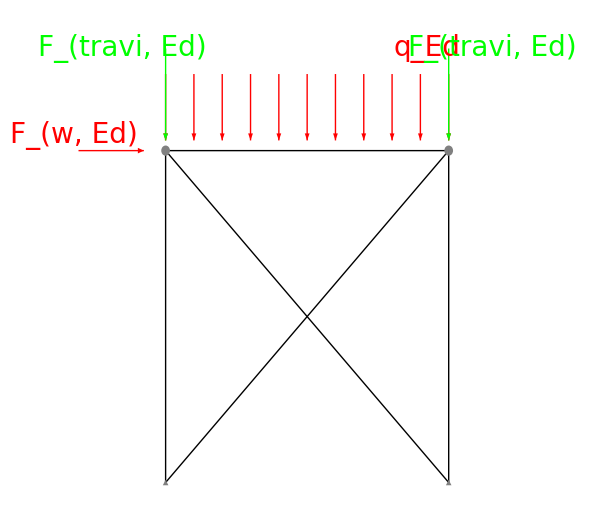

```mathematica
apph=Graphics[{Gray,Triangle[{{-0.5,-1},{0,0},{0.5,-1}}]}];
incv=Graphics[{Gray,Rectangle[{-0.5,-0.5},{0,0.5}]}];
carrh = Graphics[{
Gray,Triangle[{{-0.5,-1},{0,0},{0.5,-1}}],
Gray, Rectangle[{-.5,-1.3}, {.5, -1.8}],
Gray, Circle[{-.2,-1.15},.15],
Gray, Circle[{.2,-1.15},.15]
}];
L=6.5;h1=6.5;
portale = {Graphics[{Thick,Line[{{0,0}, {0, h1}, {L, h1}, {L,0}}]}],
Graphics[{ Thick,Line[{{0,0}, {L,h1}}]}],
Graphics[{ Thick, Line[{{L,0}, {0,h1}}]}],
Graphics[{Inset[apph, {L,0},{0,0}, Scaled[.1]]}],
Graphics[{Inset[apph, {0,0}, {0,0}, Scaled[.1]]}],
Graphics[{Red, Arrowheads[.02], Arrow[{{-2, h1}, {-.5, h1}}]}],
Graphics[{Text[Style["F_(w, Ed)",Italic, Red, 28], {-2.1, h1+.3}]}],
Graphics[{Red,Arrowheads[.02],Table[Arrow[{{i,h1+1.5},{i,h1+.2}}],{i,0,L,L/10}]}],
Graphics[Text[Style["q_Ed",Italic,Red,28],{L-.5,h2+1}]],
Graphics[{Green, Arrowheads[.02], Arrow[{{0, h1+2}, {0, h1+.2}}]}],
Graphics[{Text[Style["F_(travi, Ed)",Italic, Green, 28], {-1, h1+2}]}],
Graphics[{Green, Arrowheads[.02], Arrow[{{L, h1+2}, {L, h1+.2}}]}],
Graphics[{Text[Style["F_(travi, Ed)",Italic, Green, 28], {L+1, h1+2}]}],
Graphics[{Gray,Disk[{0,h1},.1]}],
Graphics[{Gray,Disk[{L,h1},.1]}]
};
Show[portale, ImageSize->600]
```

Il portale controventato deve avere una rigidezza almeno pari a 5 volte la rigidezza del sistema non controventato:

K_braced ≥ 5 K_unbraced

La rigidezza del sistema non controventato è

```mathematica
apph=Graphics[{Gray,Triangle[{{-0.5,-1},{0,0},{0.5,-1}}]}];
incv=Graphics[{Gray,Rectangle[{-0.5,-0.5},{0,0.5}]}];
carrh = Graphics[{
Gray,Triangle[{{-0.5,-1},{0,0},{0.5,-1}}],
Gray, Rectangle[{-.5,-1.3}, {.5, -1.8}],
Gray, Circle[{-.2,-1.15},.15],
Gray, Circle[{.2,-1.15},.15]
}];
L=6.5;h1=6.5;
portale = {
Graphics[{Thick,Line[{{0,0}, {0, h1}, {L, h1}, {L,0}}]}],
Graphics[{HatchFilling[],Black, Rectangle[{0,h1},{L, h1-.4}]}],
Graphics[{Thick,Line[{{0,h1-.4},{L, h1-.4}}]}],
Graphics[{Inset[apph, {L,0},{0,0}, Scaled[.1]]}],
Graphics[{Inset[apph, {0,0}, {0,0}, Scaled[.1]]}],
Graphics[{Red, Arrowheads[.02], Arrow[{{-2, h1-.2}, {-.5, h1-.2}}]}],
Graphics[{Text[Style["F_(w, Ed)",Italic, Red, 28], {-2.1, h1+.25}]}] 
};
Show[portale, ImageSize->600]
```

-Graphics-

-Graphics-

```mathematica
ClearAll[EJ, l, M, θ, F, δ, Ee,A, Lbr];
θ = θ/.Solve[{M*l/(3*EJ)- θ==0, -M*θ+F*θ*l==0}, {M,θ}][[1]]
δ=θ*l;
Kunbr = (2*F)/δ
{Kunbr/.EJ->Es*Jyc/.l->Lc, Kunbr/.EJ->Es*Jzc/.l->Lc}
Kbrmin = Round[5*Max[{Kunbr/.EJ->Es*Jyc/.l->Lc, Kunbr/.EJ->Es*Jzc/.l->Lc}], 1]
```

(F l^2)/(3 EJ)

(6 EJ)/l^3

{1134000/2197,1976688/10985}

2581

Allora
K_braced ≥ 5*516.2 ~= 2581 kN/m

La rigidezza del sistema controventato è 

(6*EJ_c)/L_c^3+EA/L_br*cos^2(α) ≥ 2581 kN/m

dove L_diag = √2 L_c = √2 * 6500 mm = 9192.40 mm, 
α = arctan(L/Lc)= arctan(1) = 45° => cos^2(α) = 1/2

```mathematica
Ldiag = √2*Lc;
Adiagmin = A/.Solve[6*Es*Jzc/Lc^3+(Es*A)/Ldiag*Cos[π/4]^2== Kbrmin, A][[1]]//N
```

210.204

Usando un profilo a “L” 120x120x15 con acciaio S275

```mathematica
Adiag = 33.9*10^2;
Jydiag = 444.9*10^4;
Jzdiag = Jybr;
Welydiag =  52.43*10^3;
Welzdiag = Welydiag;
fydiag = 275;

NtRddiag = Adiag*fydiag/1.05
```

887857.

La forza agente sul portale è
0.85 kN/m^2*(16.00 * 6.50 + 16.00  *1 *1/2)m^2

```mathematica
.85*(16*6.5+16*1/2)
```

95.2

La forza deve essere assorbita tutta dal controvento. Perciò:
(N^br)_(t,Rd) ≥ F_Ed 
dove in combinazione agli SLU con vento principale agli SLU

```mathematica
FEdbr = 1.5*95.2*10^3
```

142800.

```mathematica
NtRddiag > FEdbr
```

True

La snellezza adimensionale dei controventi è

```mathematica
Ncrdiag = Min[Ncr[Es, Jydiag, Ldiag], Ncr[Es, Jzdiag, Ldiag]]
λdiag = λ[Adiag, fydiag, Ncrdiag]
Ncrdiag ≥ FEdbr
```

Min[109125.,(21 Jybr π^2)/8450]

965.531 √(1/Min[109125.,(21 Jybr π^2)/8450])

Min[109125.,(21 Jybr π^2)/8450]≥142800.

Lo spostamento orizzontale sotto l’azione del vento del telaio controventato è (agli SLE)

```mathematica
Kbr = 6*Es*Jzc/Lc^3+Es*Adiag/Ldiag*Cos[π/4]^2
δbr = (FEdbr/1.5)/Kbr
If[δbr ≤ Lc/150, TextCell["Verifica sugli spostamenti orizzontali superata", "Section"], TextCell["Verifica sugli spostamenti orizzontali NON superata", "Section"]]
```

38902.2

2.44716

Verifica sugli spostamenti orizzontali superata

# Controvento di falda